# Hyperfine Zeeman shifts

P. Huft

## Setup

```mathematica
(*get from local files*)
SetDirectory[NotebookDirectory[]];
<<"../constants/rbconsts.m"
<<"../constants/physconsts.m"
SetOptions[Plot,Axes->False,Frame->{True,True,False,False},LabelStyle->Directive[Black, 14],ImageSize->Medium];
SetOptions[ListPlot,Axes->False,Frame->{True,True,False,False},LabelStyle->Directive[Black, 14],ImageSize->Medium];
SetOptions[ListLogPlot,Axes->False,Frame->{True,True,False,False},LabelStyle->Directive[Black, 14],ImageSize->Medium];
SetOptions[ListLogLogPlot,Axes->False,Frame->{True,True,False,False},LabelStyle->Directive[Black, 14],ImageSize->Medium];
EHFeV = JToeV[EHF]; 
GHzToJ[ν_]:=10^9 h ν;
GHzToeV[ν_]:=(10^9 h ν)/e ;
JToGHz[u_]:=u/(10^9 h);
JToMHz[u_]:=u/(10^6 h);
JToeV[u_]:=u/e;
eVToGHz[u_]:=e/(10^9 h)u;
KetForm[{F_,m_}]:=F,m; 
(*define some units in terms of the standard SI units*)
GHz=10^9;
MHz=10^6;
kHz=10^3;
G=10^-4;
```

## 5S and 5P Hyperfine shifts

Instantiate the functions in the 5S1/2 Hyperfine Zeeman shifts cell below before running the other subsections here.

### Diagonalize the 5S1/2 hyperfine Zeeman Hamiltonian

```mathematica
(*double letter labels for the upper state quantum numbers*)
HFZ1MatElem[I_,J_,gJ_,{F_,mF_},{FF_,mFF_},Bz_]:=Quiet[μB Bz (ClebschGordan[{F,mF},{1,0},{FF,mFF}] √(2 F +1)(-1)^(1+J+I)(gJ (-1)^F √(J (J+1)(2 J+1))SixJSymbol[{J,I,F},{FF,1,J}]+
gI(-1)^FF √(I(I+1)(2I+1))SixJSymbol[{I,J,F},{FF,1,I}]))];
KetForm[{F_,m_}]:=F,m;(*for printing nice labels*)
```

```mathematica
Clear[gF]
S = 1/2; 
L = 0; 
J = 1/2;
gJ=gL(J(J+1)+L(L+1)-S(S+1)
+gS(J(J+1)-L(L+1)+S(S+1)))/(2J(J+1));
gF[F_]:= (gJ(F(F+1)+J(J+1)-INuc(INuc+1))
+gI(F(F+1)-J(J+1)+INuc(INuc+1)))/(2F(F+1));
states = Flatten[Table[Table[{F,mF},{mF,-F,F}],{F,{2,1}}],1];
"g_(F = 1):"
gF[1]
"g_(F = 2):"
gF[2]
```

g_(F = 1):

-0.501301

g_(F = 2):

0.499311

Matrix element for transition from 1,1 to 2,1:

```mathematica
HFZ1MatElem[3/2,1/2,gJ,{1,1},{2,1},1]
```

8.03679×10^-24

```mathematica
BμW=3300/c;(*Electric field strength measured in Will group microwave antenna paper*)
(HFZ1MatElem[3/2,1/2,gJ,{1,1},{2,1},BμW]/(2 ℏ))/(2π)
```

66738.6

Compute Hamiltonians in eV to avoid ridiculously small numbers

```mathematica
dim = Length[states];
HZ1[Bz_]=Table[Table[JToeV[HFZ1MatElem[INuc,J,gJ,states[[i]],states[[j]],Bz]],{i,1,dim}],{j,1,dim}];
HAtom = Array[0&,{8,8}];
Array[(HAtom[[#,#]]=EHFeV)&,5];
HTotal[B_]=HAtom + HZ1[B];
ZShifts[B_]=SortBy[Eigenvalues[HTotal[B]],#/.B->0.1&];(*Eigenenergies [eV]*)
BList = Range[0,0.5,.1];
```

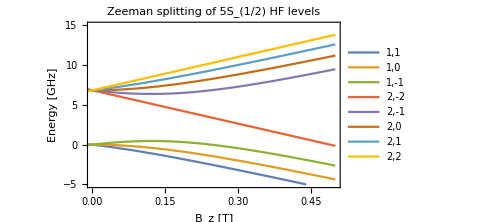

```mathematica
Bmax = 0.5; (*[T]*)
Plot[Evaluate[eVToGHz[ZShifts[B]]],{B,-Bmax,Bmax},PlotRange->{{0,Bmax},{-5,15}},PlotLabel->"Zeeman splitting of 5S_(1/2) HF levels ",FrameLabel->{"B_z [T]","Energy [GHz]"},PlotLegends->LineLegend[Join[Reverse[Array[KetForm[states[[#+5]]]&,3]],Array[KetForm[states[[#]]]&,5]],LabelStyle->Directive[Black,FontSize->10]]]
```

```mathematica
Join[Reverse[Array[KetForm[states[[#+5]]]&,3]],Array[KetForm[states[[#]]]&,5]]
```

{1,1,1,0,1,-1,2,-2,2,-1,2,0,2,1,2,2}

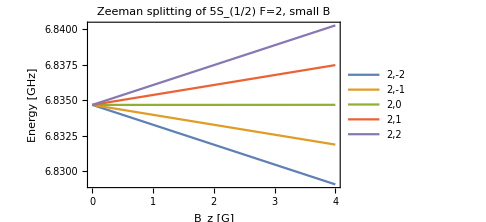

```mathematica
Bmax=4;
Plot[Evaluate[eVToGHz[ZShifts[B*10^-4][[4;;]]]],{B,0,Bmax},PlotRange->{{0,Bmax},All},PlotLabel->"Zeeman splitting of 5S_(1/2) F=2, small B",FrameLabel->{"B_z [G]","Energy [GHz]"},PlotLegends->LineLegend[Array[KetForm[states[[#]]]&,5],LabelStyle->Directive[Black,FontSize->10]]]
```

```mathematica
"MHz/G"
μB gF[2] G/(h 10^6)
```

MHz/G

0.698878

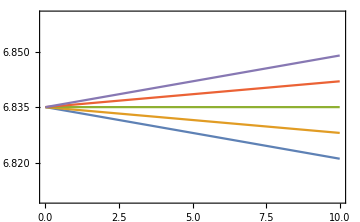

```mathematica
Plot[Evaluate[Table[μB gF[2] B G m/(h 10^9)+6.835,{m,{-2,-1,0,1,2}}]],{B,0,Bmax},PlotRange->{6.81,6.86}]
```

```mathematica
FiveSOneHalfShiftsGHz[B_]=eVToGHz[ZShifts[B]];
```

### Diagonalize the 5P3/2 hyperfine Zeeman Hamiltonian

```mathematica
(*double letter labels for the upper state quantum numbers*)
HFZ1MatElem[I_,J_,gJ_,{F_,mF_},{FF_,mFF_},Bz_]:=Quiet[μB Bz (ClebschGordan[{F,mF},{1,0},{FF,mFF}] √(2 F +1)(-1)^(1+J+I)(gJ (-1)^F √(J (J+1)(2 J+1))SixJSymbol[{J,I,F},{FF,1,J}]+
gI(-1)^FF √(I(I+1)(2I+1))SixJSymbol[{I,J,F},{FF,1,I}]))];
KetForm[{F_,m_}]:=F,m;(*for printing nice labels*)
```

```mathematica
Clear[gF]
S = 1/2; 
L = 1; 
J = 3/2;
gJ=gL(J(J+1)+L(L+1)-S(S+1)
+gS(J(J+1)-L(L+1)+S(S+1)))/(2J(J+1));
gF[F_]:= (gJ(F(F+1)+J(J+1)-INuc(INuc+1))
+gI(F(F+1)-J(J+1)+INuc(INuc+1)))/(2F(F+1));
states = Flatten[Table[Table[{F,mF},{mF,-F,F}],{F,{3,2,1,0}}],1]
```

{{3,-3},{3,-2},{3,-1},{3,0},{3,1},{3,2},{3,3},{2,-2},{2,-1},{2,0},{2,1},{2,2},{1,-1},{1,0},{1,1},{0,0}}

```mathematica
2*3+1+2*2+1+2*1+1+1
```

16

Compute Hamiltonians in eV to avoid ridiculously small numbers

```mathematica
dim = Length[states];
comOffsetMHz=72.9113;
F3GHz=193.7408*10^-3;
F2GHz=-72.9113*10^-3;
F1GHz=-229.8518*10^-3;
F0GHz=-302.0738*10^-3;
HZ1[Bz_]=Table[Table[JToeV[HFZ1MatElem[INuc,J,gJ,states[[i]],states[[j]],Bz]],{i,1,dim}],{j,1,dim}];
HAtom = Array[0&,{16,16}];
nstates=2*3+1;
nelement=0;
Array[(HAtom[[#+nelement,#+nelement]]=GHzToeV[F3GHz])&,nstates];
nelement+=nstates;
nstates=2*2+1;
Array[(HAtom[[#+nelement,#+nelement]]=GHzToeV[F2GHz])&,nstates];
nelement+=nstates;
nstates=2*1+1;
Array[(HAtom[[#+nelement,#+nelement]]=GHzToeV[F1GHz])&,nstates];
nelement+=nstates;
nstates=2*0+1;
Array[(HAtom[[#+nelement,#+nelement]]=GHzToeV[F0GHz])&,nstates];
HTotal[B_]=HAtom + HZ1[B];
ZShifts[B_]=SortBy[Eigenvalues[HTotal[B]],#/.B->4*^-4&];(*Eigenenergies [eV]*)
BList = Range[0,0.5,.1];
```

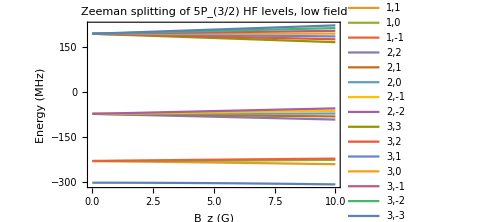

```mathematica
Bmax = 10; (*G*)
Plot[Evaluate[1000eVToGHz[ZShifts[B*10^-4]]],{B,0,Bmax},PlotRange->{{0,Bmax},All},PlotLabel->"Zeeman splitting of 5P_(3/2) HF levels, low field",FrameLabel->{"B_z (G)","Energy (MHz)"},PlotLegends->LineLegend[Reverse[Array[KetForm[states[[#]]]&,Length[states]]],LabelStyle->Directive[Black,FontSize->10]]]
```

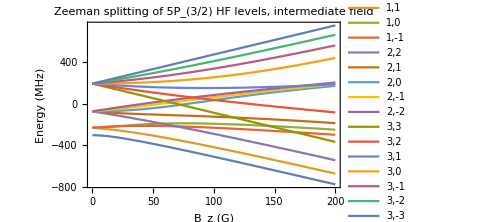

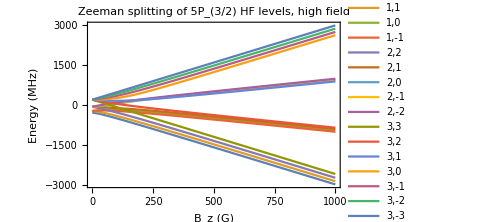

```mathematica
Bmax = 200; (*G*)
Plot[Evaluate[1000eVToGHz[ZShifts[B*10^-4]]],{B,0,Bmax},PlotRange->{{0,Bmax},All},PlotLabel->"Zeeman splitting of 5P_(3/2) HF levels, \nintermediate field",FrameLabel->{"B_z (G)","Energy (MHz)"},PlotLegends->LineLegend[Reverse[Array[KetForm[states[[#]]]&,Length[states]]],LabelStyle->Directive[Black,FontSize->10]]]
Bmax = 1000; (*G*)
Plot[Evaluate[1000eVToGHz[ZShifts[B*10^-4]]],{B,0,Bmax},PlotRange->{{0,Bmax},All},PlotLabel->"Zeeman splitting of 5P_(3/2) HF levels, high field",FrameLabel->{"B_z (G)","Energy (MHz)"},PlotLegends->LineLegend[Reverse[Array[KetForm[states[[#]]]&,Length[states]]],LabelStyle->Directive[Black,FontSize->10]]]
```

```mathematica
FivePThreeHalfShiftsGHz[B_]=eVToGHz[ZShifts[B]];
```

### Diagonalize the 5P1/2 hyperfine Zeeman Hamiltonian

```mathematica
(*double letter labels for the upper state quantum numbers*)
HFZ1MatElem[I_,J_,gJ_,{F_,mF_},{FF_,mFF_},Bz_]:=Quiet[μB Bz (ClebschGordan[{F,mF},{1,0},{FF,mFF}] √(2 F +1)(-1)^(1+J+I)(gJ (-1)^F √(J (J+1)(2 J+1))SixJSymbol[{J,I,F},{FF,1,J}]+
gI(-1)^FF √(I(I+1)(2I+1))SixJSymbol[{I,J,F},{FF,1,I}]))];
KetForm[{F_,m_}]:=F,m;(*for printing nice labels*)
```

```mathematica
Clear[gF]
S = 1/2; 
L = 1; 
J = 1/2;
gJ=gL(J(J+1)+L(L+1)-S(S+1)
+gS(J(J+1)-L(L+1)+S(S+1)))/(2J(J+1));
gF[F_]:= (gJ(F(F+1)+J(J+1)-INuc(INuc+1))
+gI(F(F+1)-J(J+1)+INuc(INuc+1)))/(2F(F+1));
states = Flatten[Table[Table[{F,mF},{mF,-F,F}],{F,{2,1}}],1]
```

{{2,-2},{2,-1},{2,0},{2,1},{2,2},{1,-1},{1,0},{1,1}}

```mathematica
Length[states]
```

8

Compute Hamiltonians in eV to avoid ridiculously small numbers

```mathematica
dim = Length[states];
F2GHz=306.246*10^-3;
F1GHz=-510.410*10^-3;
HZ1[Bz_]=Table[Table[JToeV[HFZ1MatElem[INuc,J,gJ,states[[i]],states[[j]],Bz]],{i,1,dim}],{j,1,dim}];
HAtom = Array[0&,{dim,dim}];
nelement=0;
nstates=2*2+1;
Array[(HAtom[[#+nelement,#+nelement]]=GHzToeV[F2GHz])&,nstates];
nelement+=nstates;
nstates=2*1+1;
Array[(HAtom[[#+nelement,#+nelement]]=GHzToeV[F1GHz])&,nstates];
HTotal[B_]=HAtom + HZ1[B];
ZShifts[B_]=SortBy[Eigenvalues[HTotal[B]],#/.B->4*^-4&];
(*Eigenenergies [eV]*)
```

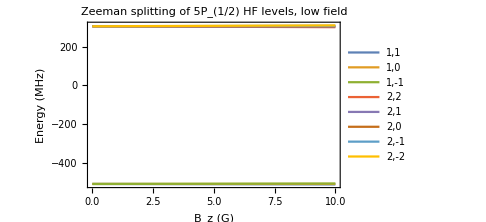

```mathematica
Bmax = 10; (*G*)
Plot[Evaluate[1000eVToGHz[ZShifts[B*10^-4]]],{B,0,Bmax},PlotRange->{{0,Bmax},All},PlotLabel->"Zeeman splitting of 5P_(1/2) HF levels, low field",FrameLabel->{"B_z (G)","Energy (MHz)"},PlotLegends->LineLegend[Reverse[Array[KetForm[states[[#]]]&,Length[states]]],LabelStyle->Directive[Black,FontSize->10]]]
```

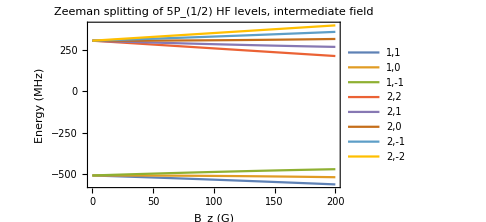

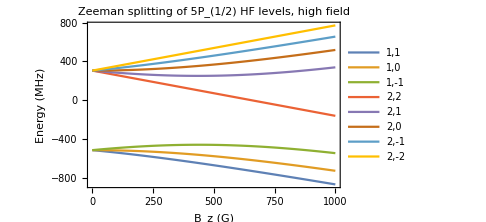

```mathematica
Bmax = 200; (*G*)
Plot[Evaluate[1000eVToGHz[ZShifts[B*10^-4]]],{B,0,Bmax},PlotRange->{{0,Bmax},All},PlotLabel->"Zeeman splitting of 5P_(1/2) HF levels, \nintermediate field",FrameLabel->{"B_z (G)","Energy (MHz)"},PlotLegends->LineLegend[Reverse[Array[KetForm[states[[#]]]&,Length[states]]],LabelStyle->Directive[Black,FontSize->10]]]
Bmax = 1000; (*G*)
Plot[Evaluate[1000eVToGHz[ZShifts[B*10^-4]]],{B,0,Bmax},PlotRange->{{0,Bmax},All},PlotLabel->"Zeeman splitting of 5P_(1/2) HF levels, high field",FrameLabel->{"B_z (G)","Energy (MHz)"},PlotLegends->LineLegend[Reverse[Array[KetForm[states[[#]]]&,Length[states]]],LabelStyle->Directive[Black,FontSize->10]]]
```

```mathematica
FivePOneHalfShiftsGHz[B_]=eVToGHz[ZShifts[B]];
```

### Differential shifts on D1 line

Having run the cells above, we have already computed the hyperfine Zeeman shifts as a function of B for the 5S1/2 and 5P1/2 levels, so we can utilize those results here.

Optical pumping is on F=1 to F’=1 on the D1 line, so we want to know what the level shifts are for the pi transitions in that group, i.e. m->m’=+/-1. First calculate with first order Zeeman shift using Lande g from Steck:

```mathematica
Bbias=9.6;(*G*)
(1/2)(0.23*1-(-0.7)*1)*Bbias
(1/2)(0.23*(-1)-(-0.7)*(-1))*Bbias
```

4.464

-4.464

Calculation with diagonalized states:

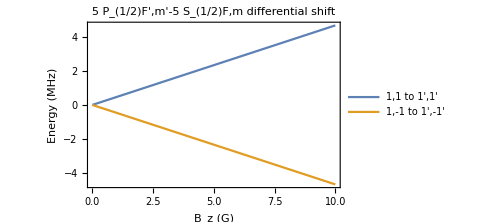

```mathematica
Bmax = 10; (*G*)
F1m1toF1m1shift[B_]=FivePOneHalfShiftsGHz[B][[1]]-FiveSOneHalfShiftsGHz[B][[1]];
F1minus1toF1minus1shift[B_]=FivePOneHalfShiftsGHz[B][[3]]-FiveSOneHalfShiftsGHz[B][[3]];
Plot[{Evaluate[1000(F1m1toF1m1shift[B*10^-4]-F1m1toF1m1shift[0])],Evaluate[1000(F1minus1toF1minus1shift[B*10^-4]-F1minus1toF1minus1shift[0])]},{B,0,Bmax},PlotRange->{{0,Bmax},All},PlotLabel->"5 P_(1/2)F',m'-5 S_(1/2)F,m\n differential shift",FrameLabel->{"B_z (G)","Energy (MHz)"},LabelStyle->Directive[Black,FontSize->10],PlotLegends->{"1,1 to 1',1'","1,-1 to 1',-1'"}]
```

```mathematica
1000(F1m1toF1m1shift[9.6*10^-4]-F1m1toF1m1shift[0])
```

4.48144

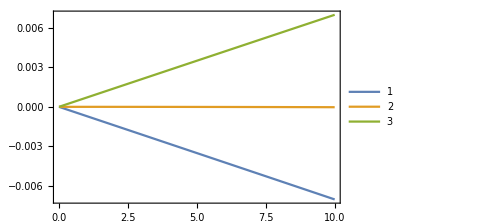

```mathematica
Plot[Evaluate[Table[FiveSOneHalfShiftsGHz[B*10^-4][[i]],{i,Range[3]}]],{B,0,Bmax},PlotLegends->Automatic]
```

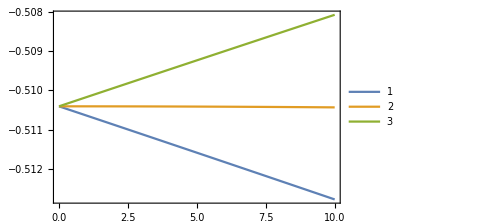

```mathematica
Plot[Evaluate[Table[FivePOneHalfShiftsGHz[B*10^-4][[i]],{i,Range[3]}]],{B,0,Bmax},PlotLegends->Automatic]
```

### Differential shifts on D2 line

Having run the cells above, we have already computed the hyperfine Zeeman shifts as a function of B for the 5S1/2 and 5P3/2 levels, so we can utilize those results here.

For the network experiment, we excite the atom from F=1,m=0 to F=0,m=0, with a bias field applied to define the quantization axis

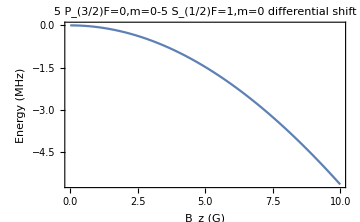

```mathematica
Bmax = 10; (*G*)
F1m0toF0m0shift[B_]=FivePThreeHalfShiftsGHz[B][[1]]-FiveSOneHalfShiftsGHz[B][[2]];
Plot[Evaluate[1000(F1m0toF0m0shift[B*10^-4]-F1m0toF0m0shift[0])],{B,0,Bmax},PlotRange->{{0,Bmax},All},PlotLabel->"5 P_(3/2)F=0,m=0-5 S_(1/2)F=1,m=0\n differential shift",FrameLabel->{"B_z (G)","Energy (MHz)"},LabelStyle->Directive[Black,FontSize->10]]
```

```mathematica
1000(F1m0toF0m0shift[0.75*10^-4]-F1m0toF0m0shift[0])
```

-0.0487086

```mathematica
Clear[gF,gJ]
S = 1/2; 
L = 0; 
J = 1/2;
gJ=gL(J(J+1)+L(L+1)-S(S+1)
+gS(J(J+1)-L(L+1)+S(S+1)))/(2J(J+1));
gF[F_]:= (gJ(F(F+1)+J(J+1)-INuc(INuc+1))
+gI(F(F+1)-J(J+1)+INuc(INuc+1)))/(2F(F+1));
FiveSOneHalfF2MHzshiftperG=μB gF[2] G/(h 10^6);
J = 3/2;
L=1;
gJJ=gL(J(J+1)+L(L+1)-S(S+1)
+gS(J(J+1)-L(L+1)+S(S+1)))/(2J(J+1));
gFF[F_]:= (gJJ(F(F+1)+J(J+1)-INuc(INuc+1))
+gI(F(F+1)-J(J+1)+INuc(INuc+1)))/(2F(F+1));FivePThreeHalvesF2MHzshiftperG=μB gFF[3] G/(h 10^6);
```

```mathematica
(3FivePThreeHalvesF2MHzshiftperG-2FiveSOneHalfF2MHzshiftperG )
```

1.39968

```mathematica
FivePThreeHalvesF2MHzshiftperG
```

0.93248

```mathematica
FiveSOneHalfF2MHzshiftperG
```

0.698878

```mathematica
-(FivePThreeHalvesF2MHzshiftperG-2FiveSOneHalfF2MHzshiftperG )1
```

-1.39968

```mathematica
(0.93+0.7)
```

1.63

```mathematica
Clear[gF,gJ]
S = 1/2; 
L = 0; 
J = 1/2;
gJ=gL(J(J+1)+L(L+1)-S(S+1)
+gS(J(J+1)-L(L+1)+S(S+1)))/(2J(J+1));
gF[F_]:= (gJ(F(F+1)+J(J+1)-INuc(INuc+1))
+gI(F(F+1)-J(J+1)+INuc(INuc+1)))/(2F(F+1));
FiveSOneHalfF2MHzshiftperG=μB gF[2] G/(h 10^6);
J = 3/2;
L=1;
gJJ=gL(J(J+1)+L(L+1)-S(S+1)
+gS(J(J+1)-L(L+1)+S(S+1)))/(2J(J+1));
gFF[F_]:= (gJJ(F(F+1)+J(J+1)-INuc(INuc+1))
+gI(F(F+1)-J(J+1)+INuc(INuc+1)))/(2F(F+1));FivePThreeHalvesF2MHzshiftperG=μB gFF[3] G/(h 10^6);
```

### Differential clock states shift

Run the 5S1/2 cell above.

m=0,m’=0 has a quadratic shift

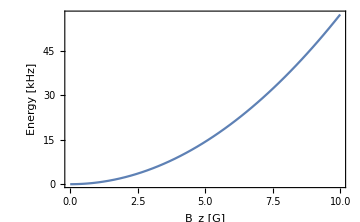

```mathematica
clockShift[B_]=FiveSOneHalfShiftsGHz[B][[6]]-FiveSOneHalfShiftsGHz[B][[2]];
Plot[(clockShift[B*10^-4]-clockShift[0])/10^-6,{B,0,10},PlotLabel->"",FrameLabel->{"B_z [G]","Energy [kHz]"},PlotRange->All]
```

```mathematica
Series[(clockShift[B*10^-4]-clockShift[0])/10^-6,{B,0,2}]
```

0.573988 B^2+O[B]^3

Expected clock state shift for 1 mK 852 nm trap and 3.2 G bias field.

```mathematica
clockShiftkHzPerG=0.574;
FORTShiftkHzPermK=-4.815;(*the light is more detuned from F=1 than F=2, so F=2 sees a stronger downward shift*)
```

```mathematica
clockShiftkHzPerG*3.2^2+FORTShiftkHzPermK*1
```

1.06276

```mathematica
4814+(clockShift[3.2*G]-clockShift[0])/10^-9
```

10691.6

```mathematica
clockShiftkHzPerG*0.1^2+FORTShiftkHzPermK*1.6
```

-7.69826

```mathematica
Table[eVToGHz[ZShifts[10^-4 B][[4]]-EHFeV-ZShifts[10^-4 B][[3]]]/10^-6,{B,-4,4}]
```

{8401.11,6300.19,4199.7,2099.63,0.,-2099.2,-4197.98,-6296.32,-8394.23}

F=2,m=0,F=1,m=1

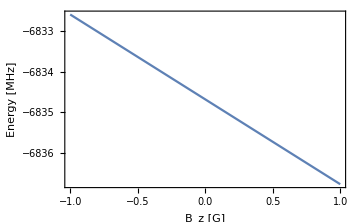

```mathematica
Plot[eVToGHz[ZShifts[10^-4 B][[4]]-EHFeV-ZShifts[10^-4 B][[7]]]/10^-3,{B,-1,1},PlotLabel->"",AxesLabel->{"B_z [G]","Energy [MHz]"}]
```

For a given Bz, the scalar Zeeman shifts are as a function of some field in the cylindrical radial direction ρ. The plot below shows the frequency offset (from the degenerate hyperfine resonance) needed to drive  F=2,m=0,F=1,m=1.

```mathematica
Manipulate[Plot[eVToGHz[ZShifts[10^-4 √(Bz^2+Bρ^2)][[4]]-EHFeV-ZShifts[10^-4 √(Bz^2+Bρ^2)][[7]]]/10^-3,{Bρ,-.4,.4},AxesLabel->{"B_ρ [G]","Energy [MHz]"},PlotLabel->"f_offset 2,0->1,1 from degenerate HF resonance",PlotRange->{2.69,2.72}],{Bz,0,4}]
```

Part::partw: Part 4 of ZShifts[0.0000399984] does not exist.

Part::partw: Part 7 of ZShifts[0.0000399984] does not exist.

Part::partw: Part 4 of ZShifts[0.0000383657] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

### Magic condition for quantum network readout basis

Using the diagonalized HF Zeeman Hamiltonian obtained above, we can plot the differential shifts for states of interest. The relevant states for the network experiment are shown below.

```mathematica
"state ordering by energy"
Join[Reverse[Array[KetForm[states[[#+5]]]&,3]],Array[KetForm[states[[#]]]&,5]]
```

state ordering by energy

{1,1,1,0,1,-1,2,-2,2,-1,2,0,2,1,2,2}

```mathematica
(*order states by shifted energy*)
statesByE=Join[Reverse[Array[states[[#+5]]&,3]],Array[states[[#]]&,5]]
```

{{1,1},{1,0},{1,-1},{2,-2},{2,-1},{2,0},{2,1},{2,2}}

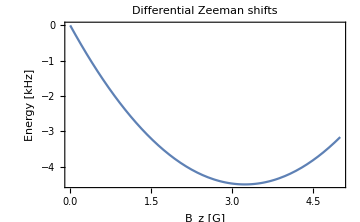

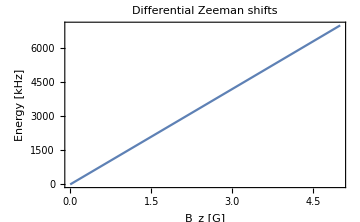

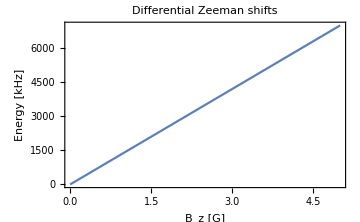

```mathematica
Bmax = 5; (*[G]*)
statePairs={{3,7},{1,7},{5,7}};
E0={(Rb87fGHz[{5,0,1/2,2}]-Rb87fGHz[{5,0,1/2,1}]),(Rb87fGHz[{5,0,1/2,2}]-Rb87fGHz[{5,0,1/2,1}]),0};
For[i=1,i<Length[statePairs]+1,i++,
pair=statePairs[[i]];
Print[
Quiet[Plot[10^6(eVToGHz[ZShifts[B 10^-4][[k]]-ZShifts[B 10^-4][[j]]]-E0[[i]])/.{k->pair[[2]],j->pair[[1]]},{B,0,Bmax},PlotLabel->"Differential Zeeman shifts",FrameLabel->{"B_z [G]","Energy [kHz]"},PlotLegends->KetForm[statesByE[[pair[[1]]]]]↔KetForm[statesByE[[pair[[2]]]]]]]]
]
```

## Excited state shifts

Instantiate the functions in the Hyperfine Zeeman shifts cell below before running the other subsections here.

### Hyperfine Zeeman shifts

### diagonalize the 87Rb 5P3/2 states Zeeman Hamiltonian

```mathematica
(*double letter labels for the upper state quantum numbers*)
HFZ1MatElem[I_,J_,gJ_,{F_,mF_},{FF_,mFF_},Bz_]:=Quiet[μB Bz (ClebschGordan[{F,mF},{1,0},{FF,mFF}] √(2 F +1)(-1)^(1+J+I)(gJ (-1)^F √(J (J+1)(2 J+1))SixJSymbol[{J,I,F},{FF,1,J}]+
gI(-1)^FF √(I(I+1)(2I+1))SixJSymbol[{I,J,F},{FF,1,I}]))];
KetForm[{F_,m_}]:=F,m;(*for printing nice labels*)
```

```mathematica
Clear[gF]
S = 1/2; 
L = 0; 
J = 1/2;
gJ=gL(J(J+1)+L(L+1)-S(S+1)
+gS(J(J+1)-L(L+1)+S(S+1)))/(2J(J+1));
gF[F_]:= (gJ(F(F+1)+J(J+1)-INuc(INuc+1))
+gI(F(F+1)-J(J+1)+INuc(INuc+1)))/(2F(F+1));
states = Flatten[Table[Table[{F,mF},{mF,-F,F}],{F,{2,1}}],1];
"g_(F = 1):"
gF[1]
"g_(F = 2):"
gF[2]
```

g_(F = 1):

-0.501301

g_(F = 2):

0.499311

Compute Hamiltonians in eV to avoid ridiculously small numbers

```mathematica
dim = Length[states];
HZ1[Bz_]=Table[Table[JToeV[HFZ1MatElem[INuc,J,gJ,states[[i]],states[[j]],Bz]],{i,1,dim}],{j,1,dim}];
HAtom = Array[0&,{8,8}];
Array[(HAtom[[#,#]]=EHFeV)&,5];
HTotal[B_]=HAtom + HZ1[B];
ZShifts[B_]=SortBy[Eigenvalues[HTotal[B]],#/.B->0.1&];(*Eigenenergies [eV]*)
BList = Range[0,0.5,.1];
```

```mathematica
Bmax = 0.5; (*[T]*)
Plot[Evaluate[eVToGHz[ZShifts[B]]],{B,-Bmax,Bmax},PlotRange->{{0,Bmax},{-5,15}},PlotLabel->"Zeeman splitting of 5S_(1/2) HF levels ",FrameLabel->{"B_z [T]","Energy [GHz]"},PlotLegends->LineLegend[Join[Reverse[Array[KetForm[states[[#+5]]]&,3]],Array[KetForm[states[[#]]]&,5]],LabelStyle->Directive[Black,FontSize->10]]]
```

-Graphics-

```mathematica
Join[Reverse[Array[KetForm[states[[#+5]]]&,3]],Array[KetForm[states[[#]]]&,5]]
```

{1,1,1,0,1,-1,2,-2,2,-1,2,0,2,1,2,2}

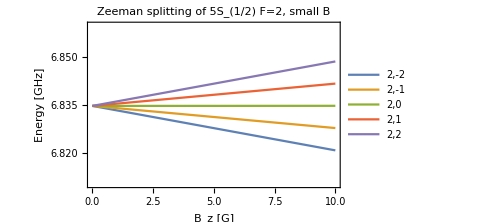

```mathematica
Bmax=10;
Plot[Evaluate[eVToGHz[ZShifts[B*10^-4][[4;;]]]],{B,0,Bmax},PlotRange->{{0,Bmax},{6.81,6.86}},PlotLabel->"Zeeman splitting of 5S_(1/2) F=2, small B",FrameLabel->{"B_z [G]","Energy [GHz]"},PlotLegends->LineLegend[Array[KetForm[states[[#]]]&,5],LabelStyle->Directive[Black,FontSize->10]]]
```

```mathematica
"MHz/G"
μB gF[2] G/(h 10^6)
```

MHz/G

0.698878

```mathematica
Plot[Evaluate[Table[μB gF[2] B G m/(h 10^9)+6.835,{m,{-2,-1,0,1,2}}]],{B,0,Bmax},PlotRange->{6.81,6.86}]
```

-Graphics-

### Differential shift for F=1,m=0 -> F’=0,m=0

m=0,m’=0 has a quadratic shift

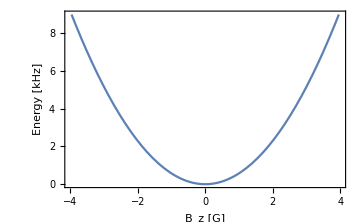

```mathematica
Plot[eVToGHz[ZShifts[10^-4 B][[6]]-EHFeV-ZShifts[10^-4 B][[2]]]/10^-6,{B,-4,4},PlotLabel->"",FrameLabel->{"B_z [G]","Energy [kHz]"},PlotRange->{0,9}]
```

```mathematica
Table[eVToGHz[ZShifts[10^-4 B][[4]]-EHFeV-ZShifts[10^-4 B][[3]]]/10^-6,{B,-4,4}]
```

Part::partw: Part 4 of Eigenvalues[{{0.0000282891,0.,0.,0.,-3.48828×10^-14,0.,0.},{0.,0.0000282775,0.,0.,-2.00647×10^-8,0.,0.},{0.,0.,0.000028266,0.,-1.42409×10^-14,-2.31687×10^-8,0.},{0.,0.,0.,0.0000282544,0.,-2.46659×10^-14,-2.00647×10^-8},{-3.48828×10^-14,-2.00647×10^-8,-1.42409×10^-14,0.,-1.16063×10^-8,0.,0.},{0.,0.,-2.31687×10^-8,-2.46659×10^-14,0.,-1.09151×10^-12,0.},{0.,0.,0.,-2.00647×10^-8,0.,0.,1.16074×10^-8}}[-1/2500]] does not exist.

Part::partw: Part 3 of Eigenvalues[{{0.0000282891,0.,0.,0.,-3.48828×10^-14,0.,0.},{0.,0.0000282775,0.,0.,-2.00647×10^-8,0.,0.},{0.,0.,0.000028266,0.,-1.42409×10^-14,-2.31687×10^-8,0.},{0.,0.,0.,0.0000282544,0.,-2.46659×10^-14,-2.00647×10^-8},{-3.48828×10^-14,-2.00647×10^-8,-1.42409×10^-14,0.,-1.16063×10^-8,0.,0.},{0.,0.,-2.31687×10^-8,-2.46659×10^-14,0.,-1.09151×10^-12,0.},{0.,0.,0.,-2.00647×10^-8,0.,0.,1.16074×10^-8}}[-1/2500]] does not exist.

Part::partw: Part 4 of Eigenvalues[{{0.0000282833,0.,0.,0.,-3.48828×10^-14,0.,0.},{0.,0.0000282746,0.,0.,-1.50485×10^-8,0.,0.},{0.,0.,0.000028266,0.,-1.42409×10^-14,-1.73765×10^-8,0.},{0.,0.,0.,0.0000282573,0.,-2.46659×10^-14,-1.50485×10^-8},{-3.48828×10^-14,-1.50485×10^-8,-1.42409×10^-14,0.,-8.70444×10^-9,0.,0.},{0.,0.,-1.73765×10^-8,-2.46659×10^-14,0.,-1.09151×10^-12,0.},{0.,0.,0.,-1.50485×10^-8,0.,0.,8.70554×10^-9}}[-3/10000]] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{2.41799×10^11 (-0.000028266-Eigenvalues[{{0.0000282891,0.,0.,0.,-3.48828×10^-14,0.,0.},{0.,0.0000282775,0.,0.,-2.00647×10^-8,0.,0.},{0.,0.,0.000028266,0.,-1.42409×10^-14,-2.31687×10^-8,0.},{0.,0.,0.,0.0000282544,0.,-2.46659×10^-14,-2.00647×10^-8},{-3.48828×10^-14,-2.00647×10^-8,-1.42409×10^-14,0.,-1.16063×10^-8,0.,0.},{0.,0.,-2.31687×10^-8,-2.46659×10^-14,0.,-1.09151×10^-12,0.},{0.,0.,0.,-2.00647×10^-8,0.,0.,1.16074×10^-8}}[-1/2500]]⟦3⟧+Eigenvalues[{{0.0000282891,0.,0.,0.,-3.48828×10^-14,0.,0.},{0.,0.0000282775,0.,0.,-2.00647×10^-8,0.,0.},{0.,0.,0.000028266,0.,-1.42409×10^-14,-2.31687×10^-8,0.},{0.,0.,0.,0.0000282544,0.,-2.46659×10^-14,-2.00647×10^-8},{-3.48828×10^-14,-2.00647×10^-8,-1.42409×10^-14,0.,-1.16063×10^-8,0.,0.},{0.,0.,-2.31687×10^-8,-2.46659×10^-14,0.,-1.09151×10^-12,0.},{0.,0.,0.,-2.00647×10^-8,0.,0.,1.16074×10^-8}}[-1/2500]]⟦4⟧),2.41799×10^11 (-0.000028266-Eigenvalues[{{0.0000282833,0.,0.,0.,-3.48828×10^-14,0.,0.},{0.,0.0000282746,0.,0.,-1.50485×10^-8,0.,0.},{0.,0.,0.000028266,0.,-1.42409×10^-14,-1.73765×10^-8,0.},{0.,0.,0.,0.0000282573,0.,-2.46659×10^-14,-1.50485×10^-8},{-3.48828×10^-14,-1.50485×10^-8,-1.42409×10^-14,0.,-8.70444×10^-9,0.,0.},{0.,0.,-1.73765×10^-8,-2.46659×10^-14,0.,-1.09151×10^-12,0.},{0.,0.,0.,-1.50485×10^-8,0.,0.,8.70554×10^-9}}[-3/10000]]⟦3⟧+Eigenvalues[{{0.0000282833,0.,0.,0.,-3.48828×10^-14,0.,0.},{0.,0.0000282746,0.,0.,-1.50485×10^-8,0.,0.},{0.,0.,0.000028266,0.,-1.42409×10^-14,-1.73765×10^-8,0.},{0.,0.,0.,0.0000282573,0.,-2.46659×10^-14,-1.50485×10^-8},{-3.48828×10^-14,-1.50485×10^-8,-1.42409×10^-14,0.,-8.70444×10^-9,0.,0.},{0.,0.,-1.73765×10^-8,-2.46659×10^-14,0.,-1.09151×10^-12,0.},{0.,0.,0.,-1.50485×10^-8,0.,0.,8.70554×10^-9}}[-3/10000]]⟦4⟧),2.41799×10^11 (-0.000028266-Eigenvalues[{{0.0000282775,0.,0.,0.,-3.48828×10^-14,0.,0.},{0.,0.0000282718,0.,0.,-1.00323×10^-8,0.,0.},{0.,0.,0.000028266,0.,-1.42409×10^-14,-1.15843×10^-8,0.},{0.,0.,0.,0.0000282602,0.,-2.46659×10^-14,-1.00323×10^-8},{-3.48828×10^-14,-1.00323×10^-8,-1.42409×10^-14,0.,-5.8026×10^-9,0.,0.},{0.,0.,-1.15843×10^-8,-2.46659×10^-14,0.,-1.09151×10^-12,0.},{0.,0.,0.,-1.00323×10^-8,0.,0.,5.80369×10^-9}}[-1/5000]]⟦3⟧+Eigenvalues[{{0.0000282775,0.,0.,0.,-3.48828×10^-14,0.,0.},{0.,0.0000282718,0.,0.,-1.00323×10^-8,0.,0.},{0.,0.,0.000028266,0.,-1.42409×10^-14,-1.15843×10^-8,0.},{0.,0.,0.,0.0000282602,0.,-2.46659×10^-14,-1.00323×10^-8},{-3.48828×10^-14,-1.00323×10^-8,-1.42409×10^-14,0.,-5.8026×10^-9,0.,0.},{0.,0.,-1.15843×10^-8,-2.46659×10^-14,0.,-1.09151×10^-12,0.},{0.,0.,0.,-1.00323×10^-8,0.,0.,5.80369×10^-9}}[-1/5000]]⟦4⟧),2.41799×10^11 (-0.000028266-Eigenvalues[{{0.0000282718,0.,0.,0.,-3.48828×10^-14,0.,0.},{0.,0.0000282689,0.,0.,-5.01617×10^-9,0.,0.},{0.,0.,0.000028266,0.,-1.42409×10^-14,-5.79217×10^-9,0.},{0.,0.,0.,0.0000282631,0.,-2.46659×10^-14,-5.01617×10^-9},{-3.48828×10^-14,-5.01617×10^-9,-1.42409×10^-14,0.,-2.90075×10^-9,0.,0.},{0.,0.,-5.79217×10^-9,-2.46659×10^-14,0.,-1.09151×10^-12,0.},{0.,0.,0.,-5.01617×10^-9,0.,0.,2.90185×10^-9}}[-1/10000]]⟦3⟧+Eigenvalues[{{0.0000282718,0.,0.,0.,-3.48828×10^-14,0.,0.},{0.,0.0000282689,0.,0.,-5.01617×10^-9,0.,0.},{0.,0.,0.000028266,0.,-1.42409×10^-14,-5.79217×10^-9,0.},{0.,0.,0.,0.0000282631,0.,-2.46659×10^-14,-5.01617×10^-9},{-3.48828×10^-14,-5.01617×10^-9,-1.42409×10^-14,0.,-2.90075×10^-9,0.,0.},{0.,0.,-5.79217×10^-9,-2.46659×10^-14,0.,-1.09151×10^-12,0.},{0.,0.,0.,-5.01617×10^-9,0.,0.,2.90185×10^-9}}[-1/10000]]⟦4⟧),2.41799×10^11 (-0.000028266-Eigenvalues[{{0.000028266,0.,0.,0.,-3.48828×10^-14,0.,0.},{0.,0.000028266,0.,0.,0.,0.,0.},{0.,0.,0.000028266,0.,-1.42409×10^-14,0.,0.},{0.,0.,0.,0.000028266,0.,-2.46659×10^-14,0.},{-3.48828×10^-14,0.,-1.42409×10^-14,0.,1.09151×10^-12,0.,0.},{0.,0.,0.,-2.46659×10^-14,0.,-1.09151×10^-12,0.},{0.,0.,0.,0.,0.,0.,0.}}[0]]⟦3⟧+Eigenvalues[{{0.000028266,0.,0.,0.,-3.48828×10^-14,0.,0.},{0.,0.000028266,0.,0.,0.,0.,0.},{0.,0.,0.000028266,0.,-1.42409×10^-14,0.,0.},{0.,0.,0.,0.000028266,0.,-2.46659×10^-14,0.},{-3.48828×10^-14,0.,-1.42409×10^-14,0.,1.09151×10^-12,0.,0.},{0.,0.,0.,-2.46659×10^-14,0.,-1.09151×10^-12,0.},{0.,0.,0.,0.,0.,0.,0.}}[0]]⟦4⟧),2.41799×10^11 (-0.000028266-Eigenvalues[{{0.0000282602,0.,0.,0.,-3.48828×10^-14,0.,0.},{0.,0.0000282631,0.,0.,5.01617×10^-9,0.,0.},{0.,0.,0.000028266,0.,-1.42409×10^-14,5.79217×10^-9,0.},{0.,0.,0.,0.0000282689,0.,-2.46659×10^-14,5.01617×10^-9},{-3.48828×10^-14,5.01617×10^-9,-1.42409×10^-14,0.,2.90294×10^-9,0.,0.},{0.,0.,5.79217×10^-9,-2.46659×10^-14,0.,-1.09151×10^-12,0.},{0.,0.,0.,5.01617×10^-9,0.,0.,-2.90185×10^-9}}[1/10000]]⟦3⟧+Eigenvalues[{{0.0000282602,0.,0.,0.,-3.48828×10^-14,0.,0.},{0.,0.0000282631,0.,0.,5.01617×10^-9,0.,0.},{0.,0.,0.000028266,0.,-1.42409×10^-14,5.79217×10^-9,0.},{0.,0.,0.,0.0000282689,0.,-2.46659×10^-14,5.01617×10^-9},{-3.48828×10^-14,5.01617×10^-9,-1.42409×10^-14,0.,2.90294×10^-9,0.,0.},{0.,0.,5.79217×10^-9,-2.46659×10^-14,0.,-1.09151×10^-12,0.},{0.,0.,0.,5.01617×10^-9,0.,0.,-2.90185×10^-9}}[1/10000]]⟦4⟧),2.41799×10^11 (-0.000028266-Eigenvalues[{{0.0000282544,0.,0.,0.,-3.48828×10^-14,0.,0.},{0.,0.0000282602,0.,0.,1.00323×10^-8,0.,0.},{0.,0.,0.000028266,0.,-1.42409×10^-14,1.15843×10^-8,0.},{0.,0.,0.,0.0000282718,0.,-2.46659×10^-14,1.00323×10^-8},{-3.48828×10^-14,1.00323×10^-8,-1.42409×10^-14,0.,5.80478×10^-9,0.,0.},{0.,0.,1.15843×10^-8,-2.46659×10^-14,0.,-1.09151×10^-12,0.},{0.,0.,0.,1.00323×10^-8,0.,0.,-5.80369×10^-9}}[1/5000]]⟦3⟧+Eigenvalues[{{0.0000282544,0.,0.,0.,-3.48828×10^-14,0.,0.},{0.,0.0000282602,0.,0.,1.00323×10^-8,0.,0.},{0.,0.,0.000028266,0.,-1.42409×10^-14,1.15843×10^-8,0.},{0.,0.,0.,0.0000282718,0.,-2.46659×10^-14,1.00323×10^-8},{-3.48828×10^-14,1.00323×10^-8,-1.42409×10^-14,0.,5.80478×10^-9,0.,0.},{0.,0.,1.15843×10^-8,-2.46659×10^-14,0.,-1.09151×10^-12,0.},{0.,0.,0.,1.00323×10^-8,0.,0.,-5.80369×10^-9}}[1/5000]]⟦4⟧),2.41799×10^11 (-0.000028266-Eigenvalues[{{0.0000282486,0.,0.,0.,-3.48828×10^-14,0.,0.},{0.,0.0000282573,0.,0.,1.50485×10^-8,0.,0.},{0.,0.,0.000028266,0.,-1.42409×10^-14,1.73765×10^-8,0.},{0.,0.,0.,0.0000282746,0.,-2.46659×10^-14,1.50485×10^-8},{-3.48828×10^-14,1.50485×10^-8,-1.42409×10^-14,0.,8.70663×10^-9,0.,0.},{0.,0.,1.73765×10^-8,-2.46659×10^-14,0.,-1.09151×10^-12,0.},{0.,0.,0.,1.50485×10^-8,0.,0.,-8.70554×10^-9}}[3/10000]]⟦3⟧+Eigenvalues[{{0.0000282486,0.,0.,0.,-3.48828×10^-14,0.,0.},{0.,0.0000282573,0.,0.,1.50485×10^-8,0.,0.},{0.,0.,0.000028266,0.,-1.42409×10^-14,1.73765×10^-8,0.},{0.,0.,0.,0.0000282746,0.,-2.46659×10^-14,1.50485×10^-8},{-3.48828×10^-14,1.50485×10^-8,-1.42409×10^-14,0.,8.70663×10^-9,0.,0.},{0.,0.,1.73765×10^-8,-2.46659×10^-14,0.,-1.09151×10^-12,0.},{0.,0.,0.,1.50485×10^-8,0.,0.,-8.70554×10^-9}}[3/10000]]⟦4⟧),2.41799×10^11 (-0.000028266-Eigenvalues[{{0.0000282429,0.,0.,0.,-3.48828×10^-14,0.,0.},{0.,0.0000282544,0.,0.,2.00647×10^-8,0.,0.},{0.,0.,0.000028266,0.,-1.42409×10^-14,2.31687×10^-8,0.},{0.,0.,0.,0.0000282775,0.,-2.46659×10^-14,2.00647×10^-8},{-3.48828×10^-14,2.00647×10^-8,-1.42409×10^-14,0.,1.16085×10^-8,0.,0.},{0.,0.,2.31687×10^-8,-2.46659×10^-14,0.,-1.09151×10^-12,0.},{0.,0.,0.,2.00647×10^-8,0.,0.,-1.16074×10^-8}}[1/2500]]⟦3⟧+Eigenvalues[{{0.0000282429,0.,0.,0.,-3.48828×10^-14,0.,0.},{0.,0.0000282544,0.,0.,2.00647×10^-8,0.,0.},{0.,0.,0.000028266,0.,-1.42409×10^-14,2.31687×10^-8,0.},{0.,0.,0.,0.0000282775,0.,-2.46659×10^-14,2.00647×10^-8},{-3.48828×10^-14,2.00647×10^-8,-1.42409×10^-14,0.,1.16085×10^-8,0.,0.},{0.,0.,2.31687×10^-8,-2.46659×10^-14,0.,-1.09151×10^-12,0.},{0.,0.,0.,2.00647×10^-8,0.,0.,-1.16074×10^-8}}[1/2500]]⟦4⟧)}

F=2,m=0,F=1,m=1

```mathematica
Plot[eVToGHz[ZShifts[10^-4 B][[4]]-EHFeV-ZShifts[10^-4 B][[7]]]/10^-3,{B,-1,1},PlotLabel->"",AxesLabel->{"B_z [G]","Energy [MHz]"}]
```

Part::partw: Part 4 of Eigenvalues[{{0.0000282718,0.,0.,0.,-3.48828×10^-14,0.,0.},{0.,0.0000282689,0.,0.,-5.01596×10^-9,0.,0.},{0.,0.,0.000028266,0.,-1.42409×10^-14,-5.79193×10^-9,0.},{0.,0.,0.,0.0000282631,0.,-2.46659×10^-14,-5.01596×10^-9},{-3.48828×10^-14,-5.01596×10^-9,-1.42409×10^-14,0.,-2.90064×10^-9,0.,0.},{0.,0.,-5.79193×10^-9,-2.46659×10^-14,0.,-1.09151×10^-12,0.},{0.,0.,0.,-5.01596×10^-9,0.,0.,2.90173×10^-9}}[-0.0000999959]] does not exist.

Part::partw: Part 7 of Eigenvalues[{{0.0000282718,0.,0.,0.,-3.48828×10^-14,0.,0.},{0.,0.0000282689,0.,0.,-5.01596×10^-9,0.,0.},{0.,0.,0.000028266,0.,-1.42409×10^-14,-5.79193×10^-9,0.},{0.,0.,0.,0.0000282631,0.,-2.46659×10^-14,-5.01596×10^-9},{-3.48828×10^-14,-5.01596×10^-9,-1.42409×10^-14,0.,-2.90064×10^-9,0.,0.},{0.,0.,-5.79193×10^-9,-2.46659×10^-14,0.,-1.09151×10^-12,0.},{0.,0.,0.,-5.01596×10^-9,0.,0.,2.90173×10^-9}}[-0.0000999959]] does not exist.

Part::partw: Part 4 of Eigenvalues[{{0.0000282715,0.,0.,0.,-3.48828×10^-14,0.,0.},{0.,0.0000282687,0.,0.,-4.81122×10^-9,0.,0.},{0.,0.,0.000028266,0.,-1.42409×10^-14,-5.55552×10^-9,0.},{0.,0.,0.,0.0000282632,0.,-2.46659×10^-14,-4.81122×10^-9},{-3.48828×10^-14,-4.81122×10^-9,-1.42409×10^-14,0.,-2.78219×10^-9,0.,0.},{0.,0.,-5.55552×10^-9,-2.46659×10^-14,0.,-1.09151×10^-12,0.},{0.,0.,0.,-4.81122×10^-9,0.,0.,2.78328×10^-9}}[-0.0000959143]] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

-Graphics-

For a given Bz, the scalar Zeeman shifts are as a function of some field in the cylindrical radial direction ρ. The plot below shows the frequency offset (from the degenerate hyperfine resonance) needed to drive  F=2,m=0,F=1,m=1.

```mathematica
Manipulate[Plot[eVToGHz[ZShifts[10^-4 √(Bz^2+Bρ^2)][[4]]-EHFeV-ZShifts[10^-4 √(Bz^2+Bρ^2)][[7]]]/10^-3,{Bρ,-.4,.4},AxesLabel->{"B_ρ [G]","Energy [MHz]"},PlotLabel->"f_offset 2,0->1,1 from degenerate HF resonance",PlotRange->{2.69,2.72}],{Bz,0,4}]
```

Part::partw: Part 4 of ZShifts[0.0000399984] does not exist.

Part::partw: Part 7 of ZShifts[0.0000399984] does not exist.

Part::partw: Part 4 of ZShifts[0.0000383657] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 4 of ZShifts[0.0000399984] does not exist.

Part::partw: Part 7 of ZShifts[0.0000399984] does not exist.

Part::partw: Part 4 of ZShifts[0.0000383657] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 4 of ZShifts[0.0000399984] does not exist.

Part::partw: Part 7 of ZShifts[0.0000399984] does not exist.

Part::partw: Part 4 of ZShifts[0.0000383657] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 4 of ZShifts[0.0000399984] does not exist.

Part::partw: Part 7 of ZShifts[0.0000399984] does not exist.

Part::partw: Part 4 of ZShifts[0.0000383657] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

### Magic condition for quantum network readout basis

Using the diagonalized HF Zeeman Hamiltonian obtained above, we can plot the differential shifts for states of interest. The relevant states for the network experiment are shown below.

```mathematica
"state ordering by energy"
Join[Reverse[Array[KetForm[states[[#+5]]]&,3]],Array[KetForm[states[[#]]]&,5]]
```

state ordering by energy

{1,1,1,0,1,-1,2,-2,2,-1,2,0,2,1,2,2}

```mathematica
(*order states by shifted energy*)
statesByE=Join[Reverse[Array[states[[#+5]]&,3]],Array[states[[#]]&,5]]
```

{{1,1},{1,0},{1,-1},{2,-2},{2,-1},{2,0},{2,1},{2,2}}

```mathematica
Bmax = 5; (*[G]*)
statePairs={{3,7},{1,7},{5,7}};
E0={(Rb87fGHz[{5,0,1/2,2}]-Rb87fGHz[{5,0,1/2,1}]),(Rb87fGHz[{5,0,1/2,2}]-Rb87fGHz[{5,0,1/2,1}]),0};
For[i=1,i<Length[statePairs]+1,i++,
pair=statePairs[[i]];
Print[
Quiet[Plot[10^6(eVToGHz[ZShifts[B 10^-4][[k]]-ZShifts[B 10^-4][[j]]]-E0[[i]])/.{k->pair[[2]],j->pair[[1]]},{B,0,Bmax},PlotLabel->"Differential Zeeman shifts",FrameLabel->{"B_z [G]","Energy [kHz]"},PlotLegends->KetForm[statesByE[[pair[[1]]]]]↔KetForm[statesByE[[pair[[2]]]]]]]]
]
```

-Graphics-

-Graphics-

-Graphics-

## Mitigating magnetic sensitivity with microwave dressing

Run the Ground State Shift cell Hyperfine Zeeman Shifts first

Todo. See “Controlling the magnetic-field sensitivity of atomic-clock states by microwave dressing” by the Fortagh group.

```mathematica
-Graphics-;
```

```mathematica
"state ordering by energy"
Join[Reverse[Array[KetForm[states[[#+5]]]&,3]],Array[KetForm[states[[#]]]&,5]]
```

state ordering by energy

{1,1,1,0,1,-1,2,-2,2,-1,2,0,2,1,2,2}

```mathematica
(*order states by shifted energy*)
statesByE=Join[Reverse[Array[states[[#+5]]&,3]],Array[states[[#]]&,5]]
```

{{1,1},{1,0},{1,-1},{2,-2},{2,-1},{2,0},{2,1},{2,2}}

### verify eqs 7-11

```mathematica
(*verify eqs. 1 and 2 from the Fortagh paper*)
eVToGHz[Series[ZShifts[B][[3]],{B,0,2}]]GHz
eVToGHz[Series[ZShifts[B][[7]],{B,0,2}]]GHz
```

Part::partw: Part 3 of Eigenvalues[{{0.000028266-0.0000578065 B,0.,0.,0.,-3.48828×10^-14,0.,0.},{0.,0.000028266-0.0000289033 B,0.,0.,0.0000501617 B,0.,0.},{0.,0.,0.000028266,0.,-1.42409×10^-14,0.0000579217 B,0.},{0.,0.,0.,0.000028266+0.0000289033 B,0.,-2.46659×10^-14,0.0000501617 B},{-3.48828×10^-14,0.0000501617 B,-1.42409×10^-14,0.,1.09151×10^-12+0.0000290185 B,0.,0.},{0.,0.,0.0000579217 B,-2.46659×10^-14,0.,-1.09151×10^-12,0.},{0.,0.,0.,0.0000501617 B,0.,0.,-0.0000290185 B}}[B]] does not exist.

2.41799×10^14 Eigenvalues[{{0.000028266-0.0000578065 B,0.,0.,0.,-3.48828×10^-14,0.,0.},{0.,0.000028266-0.0000289033 B,0.,0.,0.0000501617 B,0.,0.},{0.,0.,0.000028266,0.,-1.42409×10^-14,0.0000579217 B,0.},{0.,0.,0.,0.000028266+0.0000289033 B,0.,-2.46659×10^-14,0.0000501617 B},{-3.48828×10^-14,0.0000501617 B,-1.42409×10^-14,0.,1.09151×10^-12+0.0000290185 B,0.,0.},{0.,0.,0.0000579217 B,-2.46659×10^-14,0.,-1.09151×10^-12,0.},{0.,0.,0.,0.0000501617 B,0.,0.,-0.0000290185 B}}[B]]⟦3⟧

Part::partw: Part 7 of Eigenvalues[{{0.000028266-0.0000578065 B,0.,0.,0.,-3.48828×10^-14,0.,0.},{0.,0.000028266-0.0000289033 B,0.,0.,0.0000501617 B,0.,0.},{0.,0.,0.000028266,0.,-1.42409×10^-14,0.0000579217 B,0.},{0.,0.,0.,0.000028266+0.0000289033 B,0.,-2.46659×10^-14,0.0000501617 B},{-3.48828×10^-14,0.0000501617 B,-1.42409×10^-14,0.,1.09151×10^-12+0.0000290185 B,0.,0.},{0.,0.,0.0000579217 B,-2.46659×10^-14,0.,-1.09151×10^-12,0.},{0.,0.,0.,0.0000501617 B,0.,0.,-0.0000290185 B}}[B]] does not exist.

2.41799×10^14 Eigenvalues[{{0.000028266-0.0000578065 B,0.,0.,0.,-3.48828×10^-14,0.,0.},{0.,0.000028266-0.0000289033 B,0.,0.,0.0000501617 B,0.,0.},{0.,0.,0.000028266,0.,-1.42409×10^-14,0.0000579217 B,0.},{0.,0.,0.,0.000028266+0.0000289033 B,0.,-2.46659×10^-14,0.0000501617 B},{-3.48828×10^-14,0.0000501617 B,-1.42409×10^-14,0.,1.09151×10^-12+0.0000290185 B,0.,0.},{0.,0.,0.0000579217 B,-2.46659×10^-14,0.,-1.09151×10^-12,0.},{0.,0.,0.,0.0000501617 B,0.,0.,-0.0000290185 B}}[B]]⟦7⟧

```mathematica
(*this agrees to within a percent with the Fortagh values*)
μ1=2π 7.00632903759789*^9 ;(*Hz/T*)
"μ1/2π (Hz/G)"
μ1/(2π)/(kHz/G)
μ2=2π 6.978516230857793*^9 ; (*Hz/T*)
"μ1/2π (Hz/G)"
μ2/(2π)/(kHz/G)
β=2π 1/3 2.1461409583667313*^10;(*Hz/T^2*)
"β/2π (Hz/G^2)"
β/(2π)/(kHz/G^2)
```

μ1/2π (Hz/G)

700.633

μ1/2π (Hz/G)

697.852

β/2π (Hz/G^2)

0.071538

```mathematica
(*calculate the transition rate coefficients given in the figure above*)
Inuc=3/2;
S = 1/2; 
L = 0; 
J = 1/2;
gJ=gL(J(J+1)+L(L+1)-S(S+1)
+gS(J(J+1)-L(L+1)+S(S+1)))/(2J(J+1));
gF = (gJ(F(F+1)+J(J+1)-Inuc(Inuc+1))
+gI(F(F+1)-J(J+1)+Inuc(Inuc+1)))/(2F(F+1));
F= 1;FF=2;
```

My coefficients for the Rabi frequencies match those in the Fortagh paper if use the following definition of  Ωdressing. Their definition  is different from mine because they lump the amplitude for the σ component of the driving field and the typical factor of 1/2 in the matrix element into the definition of Ωdressing, hence the factor of 1/(2 √2) in theirs. I pull these out to make them explicit.

```mathematica
Ωdressing=μB gF B/ℏ;
mF =-1;mFF=-2;
Bσ=B/(√2);(*The magnitude of the dressing B field times σ_-Subscript[π, x]*)
"2,-2H1,-1/Ωdressing"
1/ℏ μB Bσ ClebschGordan[{F,mF},{1,mFF-mF},{FF,mFF}] √(2 F +1)(-1)^(1+J+Inuc)(gJ (-1)^F √(J (J+1)(2 J+1))SixJSymbol[{J,Inuc,F},{FF,1,J}]+
gI(-1)^FF √(Inuc(Inuc+1)(2Inuc+1))SixJSymbol[{Inuc,J,F},{FF,1,Inuc}])/Ωdressing
mF =-1;mFF=0;
Bσ=B/(√2);(*The magnitude of the dressing B field times σ_+Subscript[π, x]*)
"2,-1H1,0/Ωdressing"
1/ℏ μB Bσ ClebschGordan[{F,mF},{1,mFF-mF},{FF,mFF}] √(2 F +1)(-1)^(1+J+Inuc)(gJ (-1)^F √(J (J+1)(2 J+1))SixJSymbol[{J,Inuc,F},{FF,1,J}]+
gI(-1)^FF √(Inuc(Inuc+1)(2Inuc+1))SixJSymbol[{Inuc,J,F},{FF,1,Inuc}])/Ωdressing
mF =0;mFF=1;
Bσ=B/(√2);(*The magnitude of the dressing B field times σ_+Subscript[π, x]*)
"2,0H1,1/Ωdressing"
1/ℏ μB Bσ ClebschGordan[{F,mF},{1,mFF-mF},{FF,mFF}] √(2 F +1)(-1)^(1+J+Inuc)(gJ (-1)^F √(J (J+1)(2 J+1))SixJSymbol[{J,Inuc,F},{FF,1,J}]+
gI(-1)^FF √(Inuc(Inuc+1)(2Inuc+1))SixJSymbol[{Inuc,J,F},{FF,1,Inuc}])/Ωdressing
```

2,-2H1,-1/Ωdressing

-1.72861

2,-1H1,0/Ωdressing

-0.705703

2,0H1,1/Ωdressing

-1.22231

Solve for the dressed eigenergies. The dressing field does not directly couple the states to each other, so we have two separate Hamiltonians to diagonalize. The relevant energies are defined below.

```mathematica
"2,-2"
E4=10^9 eVToGHz[Series[ZShifts[B][[4]],{B,0,2}]]//Normal
"2,0"
E6=10^9 eVToGHz[Series[ZShifts[B][[6]],{B,0,2}]]//Normal
"1,0"
E2=10^9 eVToGHz[Series[ZShifts[B][[2]],{B,0,2}]]//Normal
(*"1,-1 0"*)
E3=10^9 eVToGHz[Series[ZShifts[B][[3]],{B,0,2}]]//Normal;
(*"2,1 1"*)
E7=10^9 eVToGHz[Series[ZShifts[B][[7]],{B,0,2}]]//Normal;
```

2,-2

Part::partw: Part 4 of Eigenvalues[{{0.000028266-0.0000578065 B,0.,0.,0.,-3.48828×10^-14,0.,0.},{0.,0.000028266-0.0000289033 B,0.,0.,0.0000501617 B,0.,0.},{0.,0.,0.000028266,0.,-1.42409×10^-14,0.0000579217 B,0.},{0.,0.,0.,0.000028266+0.0000289033 B,0.,-2.46659×10^-14,0.0000501617 B},{-3.48828×10^-14,0.0000501617 B,-1.42409×10^-14,0.,1.09151×10^-12+0.0000290185 B,0.,0.},{0.,0.,0.0000579217 B,-2.46659×10^-14,0.,-1.09151×10^-12,0.},{0.,0.,0.,0.0000501617 B,0.,0.,-0.0000290185 B}}[B]] does not exist.

2.41799×10^14 Eigenvalues[{{0.000028266-0.0000578065 B,0.,0.,0.,-3.48828×10^-14,0.,0.},{0.,0.000028266-0.0000289033 B,0.,0.,0.0000501617 B,0.,0.},{0.,0.,0.000028266,0.,-1.42409×10^-14,0.0000579217 B,0.},{0.,0.,0.,0.000028266+0.0000289033 B,0.,-2.46659×10^-14,0.0000501617 B},{-3.48828×10^-14,0.0000501617 B,-1.42409×10^-14,0.,1.09151×10^-12+0.0000290185 B,0.,0.},{0.,0.,0.0000579217 B,-2.46659×10^-14,0.,-1.09151×10^-12,0.},{0.,0.,0.,0.0000501617 B,0.,0.,-0.0000290185 B}}[B]]⟦4⟧

2,0

Part::partw: Part 6 of Eigenvalues[{{0.000028266-0.0000578065 B,0.,0.,0.,-3.48828×10^-14,0.,0.},{0.,0.000028266-0.0000289033 B,0.,0.,0.0000501617 B,0.,0.},{0.,0.,0.000028266,0.,-1.42409×10^-14,0.0000579217 B,0.},{0.,0.,0.,0.000028266+0.0000289033 B,0.,-2.46659×10^-14,0.0000501617 B},{-3.48828×10^-14,0.0000501617 B,-1.42409×10^-14,0.,1.09151×10^-12+0.0000290185 B,0.,0.},{0.,0.,0.0000579217 B,-2.46659×10^-14,0.,-1.09151×10^-12,0.},{0.,0.,0.,0.0000501617 B,0.,0.,-0.0000290185 B}}[B]] does not exist.

2.41799×10^14 Eigenvalues[{{0.000028266-0.0000578065 B,0.,0.,0.,-3.48828×10^-14,0.,0.},{0.,0.000028266-0.0000289033 B,0.,0.,0.0000501617 B,0.,0.},{0.,0.,0.000028266,0.,-1.42409×10^-14,0.0000579217 B,0.},{0.,0.,0.,0.000028266+0.0000289033 B,0.,-2.46659×10^-14,0.0000501617 B},{-3.48828×10^-14,0.0000501617 B,-1.42409×10^-14,0.,1.09151×10^-12+0.0000290185 B,0.,0.},{0.,0.,0.0000579217 B,-2.46659×10^-14,0.,-1.09151×10^-12,0.},{0.,0.,0.,0.0000501617 B,0.,0.,-0.0000290185 B}}[B]]⟦6⟧

1,0

Part::partw: Part 2 of Eigenvalues[{{0.000028266-0.0000578065 B,0.,0.,0.,-3.48828×10^-14,0.,0.},{0.,0.000028266-0.0000289033 B,0.,0.,0.0000501617 B,0.,0.},{0.,0.,0.000028266,0.,-1.42409×10^-14,0.0000579217 B,0.},{0.,0.,0.,0.000028266+0.0000289033 B,0.,-2.46659×10^-14,0.0000501617 B},{-3.48828×10^-14,0.0000501617 B,-1.42409×10^-14,0.,1.09151×10^-12+0.0000290185 B,0.,0.},{0.,0.,0.0000579217 B,-2.46659×10^-14,0.,-1.09151×10^-12,0.},{0.,0.,0.,0.0000501617 B,0.,0.,-0.0000290185 B}}[B]] does not exist.

2.41799×10^14 Eigenvalues[{{0.000028266-0.0000578065 B,0.,0.,0.,-3.48828×10^-14,0.,0.},{0.,0.000028266-0.0000289033 B,0.,0.,0.0000501617 B,0.,0.},{0.,0.,0.000028266,0.,-1.42409×10^-14,0.0000579217 B,0.},{0.,0.,0.,0.000028266+0.0000289033 B,0.,-2.46659×10^-14,0.0000501617 B},{-3.48828×10^-14,0.0000501617 B,-1.42409×10^-14,0.,1.09151×10^-12+0.0000290185 B,0.,0.},{0.,0.,0.0000579217 B,-2.46659×10^-14,0.,-1.09151×10^-12,0.},{0.,0.,0.,0.0000501617 B,0.,0.,-0.0000290185 B}}[B]]⟦2⟧

Part::partw: Part 3 of Eigenvalues[{{0.000028266-0.0000578065 B,0.,0.,0.,-3.48828×10^-14,0.,0.},{0.,0.000028266-0.0000289033 B,0.,0.,0.0000501617 B,0.,0.},{0.,0.,0.000028266,0.,-1.42409×10^-14,0.0000579217 B,0.},{0.,0.,0.,0.000028266+0.0000289033 B,0.,-2.46659×10^-14,0.0000501617 B},{-3.48828×10^-14,0.0000501617 B,-1.42409×10^-14,0.,1.09151×10^-12+0.0000290185 B,0.,0.},{0.,0.,0.0000579217 B,-2.46659×10^-14,0.,-1.09151×10^-12,0.},{0.,0.,0.,0.0000501617 B,0.,0.,-0.0000290185 B}}[B]] does not exist.

Part::partw: Part 7 of Eigenvalues[{{0.000028266-0.0000578065 B,0.,0.,0.,-3.48828×10^-14,0.,0.},{0.,0.000028266-0.0000289033 B,0.,0.,0.0000501617 B,0.,0.},{0.,0.,0.000028266,0.,-1.42409×10^-14,0.0000579217 B,0.},{0.,0.,0.,0.000028266+0.0000289033 B,0.,-2.46659×10^-14,0.0000501617 B},{-3.48828×10^-14,0.0000501617 B,-1.42409×10^-14,0.,1.09151×10^-12+0.0000290185 B,0.,0.},{0.,0.,0.0000579217 B,-2.46659×10^-14,0.,-1.09151×10^-12,0.},{0.,0.,0.,0.0000501617 B,0.,0.,-0.0000290185 B}}[B]] does not exist.

Derive the RWA detuning expressions given by Eqs. 8,9,10. My expressions are in SI units.

```mathematica
Clear[Δdress,ωdress]
ω0=2π(EHF/h);
ω0/(2π)
Δdress=ωdress-ω0;
```

6.83468×10^9

```mathematica
Δ1=Δdress+2π( E3-E4)+ω0;
Coefficient[Δ1,B,1]/(μ1+2μ2)
Coefficient[Δ1,B,2]/(-3β)
```

0.

0.

```mathematica
Δ2=Δdress+2π(E3-E6)+ω0;
Coefficient[Δ2,B,1]/μ1
Coefficient[Δ2,B,2]/(-7β)
```

0.

0.

```mathematica
Δ3=Δdress+2π(E2-E7)+ω0
Coefficient[Δ3,B,1]/(-μ2)
Coefficient[Δ3,B,2]/(-7β)
```

0.+ωdress+2 π (2.41799×10^14 Eigenvalues[{{0.000028266-0.0000578065 B,0.,0.,0.,-3.48828×10^-14,0.,0.},{0.,0.000028266-0.0000289033 B,0.,0.,0.0000501617 B,0.,0.},{0.,0.,0.000028266,0.,-1.42409×10^-14,0.0000579217 B,0.},{0.,0.,0.,0.000028266+0.0000289033 B,0.,-2.46659×10^-14,0.0000501617 B},{-3.48828×10^-14,0.0000501617 B,-1.42409×10^-14,0.,1.09151×10^-12+0.0000290185 B,0.,0.},{0.,0.,0.0000579217 B,-2.46659×10^-14,0.,-1.09151×10^-12,0.},{0.,0.,0.,0.0000501617 B,0.,0.,-0.0000290185 B}}[B]]⟦2⟧-2.41799×10^14 Eigenvalues[{{0.000028266-0.0000578065 B,0.,0.,0.,-3.48828×10^-14,0.,0.},{0.,0.000028266-0.0000289033 B,0.,0.,0.0000501617 B,0.,0.},{0.,0.,0.000028266,0.,-1.42409×10^-14,0.0000579217 B,0.},{0.,0.,0.,0.000028266+0.0000289033 B,0.,-2.46659×10^-14,0.0000501617 B},{-3.48828×10^-14,0.0000501617 B,-1.42409×10^-14,0.,1.09151×10^-12+0.0000290185 B,0.,0.},{0.,0.,0.0000579217 B,-2.46659×10^-14,0.,-1.09151×10^-12,0.},{0.,0.,0.,0.0000501617 B,0.,0.,-0.0000290185 B}}[B]]⟦7⟧)

0.

0.

### Solve eq. 11 using coeffs defined above

Now we can compute the energy difference between the qubit states as a function of the applied dressing field strength and frequency.

```mathematica
(*this block of code isn't succeeding at getting the solutions shown in the Fig 2 legend*)
ΔEqubit=ω0+(μ2-μ1)B+6β B^2-Ωdress^2(3/Δ1+1/(2Δ2)+3/(2Δ3));
Boffset=2.7G;
{ωsoln,Ωsoln}=Transpose@Chop[Values[NSolve[{(D[ΔEqubit,B]/.B->Boffset)==0,(D[ΔEqubit,{B,2}]/.B->Boffset)==0},{ωdress,Ωdress},Reals]]];
Transpose@{Ωsoln/(2π kHz),(ωsoln-ω0)/(2π MHz)}//TableForm
```

Part::partw: Part 3 of Eigenvalues[{{0.0000282504,0.,0.,0.,-3.48828×10^-14,0.,0.},{0.,0.0000282582,0.,0.,1.35437×10^-8,0.,0.},{0.,0.,0.000028266,0.,-1.42409×10^-14,1.56389×10^-8,0.},{0.,0.,0.,0.0000282738,0.,-2.46659×10^-14,1.35437×10^-8},{-3.48828×10^-14,1.35437×10^-8,-1.42409×10^-14,0.,7.83607×10^-9,0.,0.},{0.,0.,1.56389×10^-8,-2.46659×10^-14,0.,-1.09151×10^-12,0.},{0.,0.,0.,1.35437×10^-8,0.,0.,-7.83498×10^-9}}[0.00027]] does not exist.

Part::partw: Part 4 of Eigenvalues[{{0.0000282504,0.,0.,0.,-3.48828×10^-14,0.,0.},{0.,0.0000282582,0.,0.,1.35437×10^-8,0.,0.},{0.,0.,0.000028266,0.,-1.42409×10^-14,1.56389×10^-8,0.},{0.,0.,0.,0.0000282738,0.,-2.46659×10^-14,1.35437×10^-8},{-3.48828×10^-14,1.35437×10^-8,-1.42409×10^-14,0.,7.83607×10^-9,0.,0.},{0.,0.,1.56389×10^-8,-2.46659×10^-14,0.,-1.09151×10^-12,0.},{0.,0.,0.,1.35437×10^-8,0.,0.,-7.83498×10^-9}}[0.00027]] does not exist.

Part::partw: Part 3 of Eigenvalues[{{0.0000282504,0.,0.,0.,-3.48828×10^-14,0.,0.},{0.,0.0000282582,0.,0.,1.35437×10^-8,0.,0.},{0.,0.,0.000028266,0.,-1.42409×10^-14,1.56389×10^-8,0.},{0.,0.,0.,0.0000282738,0.,-2.46659×10^-14,1.35437×10^-8},{-3.48828×10^-14,1.35437×10^-8,-1.42409×10^-14,0.,7.83607×10^-9,0.,0.},{0.,0.,1.56389×10^-8,-2.46659×10^-14,0.,-1.09151×10^-12,0.},{0.,0.,0.,1.35437×10^-8,0.,0.,-7.83498×10^-9}}[0.00027]] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

$Aborted

-21.8838 | -1.21192
21.8838 | -1.21192
17.0959 | -3.61871
-17.0959 | -3.61871
1209.06 | -0.00199736
-1209.06 | -0.00199736
224.036 | 8.03975
-224.036 | 8.03975

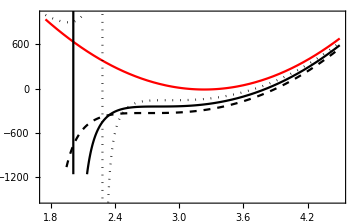

```mathematica
Show[Plot[((ΔEqubit/.Ωdress->0)-ω0+2π 4500)/( 2π)/.B->Bdc G,{Bdc,1.75,4.5},PlotStyle->Red],Plot[((ΔEqubit/.{Ωdress->2π 21.9 kHz,ωdress->ω0-2π 1.21 MHz})-ω0+2π 4500)/( 2π)/.B->Bdc G,{Bdc,1.75,4.5},PlotStyle->Directive[Dashed,Black]],Plot[((ΔEqubit/.{Ωdress->2π 16.6 kHz,ωdress->ω0-2π 1.41 MHz})-ω0+2π 4500)/( 2π)/.B->Bdc G,{Bdc,1.75,4.5},PlotStyle->Directive[Black]],
Plot[((ΔEqubit/.{Ωdress->2π 11.7 kHz,ωdress->ω0-2π 1.6 MHz})-ω0+2π 4500)/( 2π)/.B->Bdc G,{Bdc,1.75,4.5},PlotStyle->Directive[Dotted,Black]],
PlotRange->{-1500,1000}]
```

### Solve eq. 11 using coeffs defined as in text

```mathematica
(*try redefining the coefficients here as a way of diagnosing the issue*)
ω0=2π 6.8346826109 GHz;(*I defined EHF to more precision than they do.(EHF/h)*);
Δdress=ωdress-ω0;
μ1=2π*702.37kHz/G;
μ2=2π*699.58kHz/G;
β=2π*71.89/G^2;
Δ1=Δdress+(μ1+2μ2)B-3β B^2;
Δ2=Δdress+μ1 B-7β B^2;
Δ3=Δdress-μ2 B-7β B^2;
ΔEqubit=ω0+(μ2-μ1)B+6β B^2-Ωdress^2(3/Δ1+1/(2Δ2)+3/(2Δ3));
Boffset=2.7G;
{ωsoln,Ωsoln}=Transpose@Values[NSolve[{(D[ΔEqubit,B]/.B->Boffset)==0,(D[ΔEqubit,{B,2}]/.B->Boffset)==0},{ωdress,Ωdress},Reals]];
Transpose@{Ωsoln/(2π kHz),(ωsoln-ω0)/(2π MHz)}//TableForm
```

-21.8838 | -1.21192
21.8838 | -1.21192
17.0959 | -3.61871
-17.0959 | -3.61871
1209.06 | -0.00199735
-1209.06 | -0.00199735
224.036 | 8.03975
-224.036 | 8.03975

```mathematica
(*the first curve is the Breit-Rabi parabola, but I needed to add in an offset of 4500 Hz to get it to go to zero. I think they shifted this in the paper so the parabola minimum was referenced to zero*)
Show[Plot[((ΔEqubit/.Ωdress->0)-ω0+2π 4500)/( 2π)/.B->Bdc G,{Bdc,1.75,4.5},PlotStyle->Red],Plot[((ΔEqubit/.{Ωdress->2π 21.9 kHz,ωdress->ω0-2π 1.21 MHz})-ω0+2π 4500)/( 2π)/.B->Bdc G,{Bdc,1.75,4.5},PlotStyle->Directive[Dashed,Black]],Plot[((ΔEqubit/.{Ωdress->2π 16.6 kHz,ωdress->ω0-2π 1.41 MHz})-ω0+2π 4500)/( 2π)/.B->Bdc G,{Bdc,1.75,4.5},PlotStyle->Directive[Black]],
Plot[((ΔEqubit/.{Ωdress->2π 11.7 kHz,ωdress->ω0-2π 1.6 MHz})-ω0+2π 4500)/( 2π)/.B->Bdc G,{Bdc,1.75,4.5},PlotStyle->Directive[Dotted,Black]],
PlotRange->{-1500,1000}]
```

-Graphics-

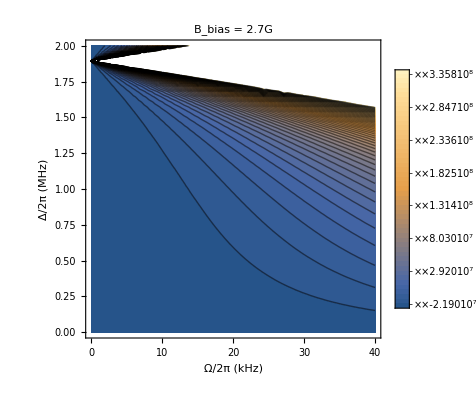

```mathematica
ContourPlot[D[ΔEqubit,B]/.{B->Boffset,Ωdress->2π ΩkHz 10^3,ωdress->ω0-2π ΔMHz 10^6},{ΩkHz,0,40},{ΔMHz,0,2},PlotLegends->Automatic,FrameLabel->{"Ω/2π (kHz)","Δ/2π (MHz)"},PlotLabel->StringForm["B_bias = ``G",Boffset/G],Contours->50]
```

### Solve with my definitions

[*] put the explicit expressions for Eq. 11 here, i.e. using the C.G. expressions to compute the dressing coupling prefactors and
[ ] Plot curve with the dressing solution for 2.8G assuming no polarization error, alongside curves with the same dressing parameters but various amounts of polarization error ϵ.
[ ] include additional terms for the shifts which result from π polarized light, where the terms for sigma light are multiplied by √(1-ϵ) and the terms with π light are multiplied by √ϵ.
[ ] Solve the modified Eq. 11 for cases in which there is a small amount of ϵ. Do solutions still exist?

```mathematica
Inuc=3/2;
S = 1/2; 
L = 0; 
J = 1/2;
gJ=gL(J(J+1)+L(L+1)-S(S+1)
+gS(J(J+1)-L(L+1)+S(S+1)))/(2J(J+1));
gF = (gJ(F(F+1)+J(J+1)-Inuc(Inuc+1))
+gI(F(F+1)-J(J+1)+Inuc(Inuc+1)))/(2F(F+1));
F= 1;FF=2;
(*The leading factor of 1/√2 is the amplitude Bσ_±Subscript[Bπ, x]*)
mF =-1;mFF=-2;
"2,-2H1,-1/(ℏ μB gF)"
c1 =1/(√2)ClebschGordan[{F,mF},{1,mFF-mF},{FF,mFF}] √(2 F +1)(-1)^(1+J+Inuc)(gJ (-1)^F √(J (J+1)(2 J+1))SixJSymbol[{J,Inuc,F},{FF,1,J}]+
gI(-1)^FF √(Inuc(Inuc+1)(2Inuc+1))SixJSymbol[{Inuc,J,F},{FF,1,Inuc}])/gF
(*2,-2H1,-1/(ℏ μB gF)*)
mF =-1;mFF=0;
"2,0H1,-1/(ℏ μB gF)"
c2= 1/(√2) ClebschGordan[{F,mF},{1,mFF-mF},{FF,mFF}] √(2 F +1)(-1)^(1+J+Inuc)(gJ (-1)^F √(J (J+1)(2 J+1))SixJSymbol[{J,Inuc,F},{FF,1,J}]+
gI(-1)^FF √(Inuc(Inuc+1)(2Inuc+1))SixJSymbol[{Inuc,J,F},{FF,1,Inuc}])/gF(*2,0H1,-1/(ℏ μB gF)*)
mF =0;mFF=1;
"2,1H1,0/(ℏ μB gF)"
c3=1/(√2) ClebschGordan[{F,mF},{1,mFF-mF},{FF,mFF}] √(2 F +1)(-1)^(1+J+Inuc)(gJ (-1)^F √(J (J+1)(2 J+1))SixJSymbol[{J,Inuc,F},{FF,1,J}]+
gI(-1)^FF √(Inuc(Inuc+1)(2Inuc+1))SixJSymbol[{Inuc,J,F},{FF,1,Inuc}])/gF(*2,1H1,0/(ℏ μB gF)*)
```

2,-2H1,-1/(ℏ μB gF)

-1.72861

2,0H1,-1/(ℏ μB gF)

-0.705703

2,1H1,0/(ℏ μB gF)

-1.22231

```mathematica
Clear[ωdress,Δdress]
E4=GHz eVToGHz[Series[ZShifts[B][[4]],{B,0,2}]]//Normal(*"2,-2"*)
E6=GHz eVToGHz[Series[ZShifts[B][[6]],{B,0,2}]]//Normal(*"2,0"*)
E2=GHz eVToGHz[Series[ZShifts[B][[2]],{B,0,2}]]//Normal(*"1,0"*)
E3=GHz eVToGHz[Series[ZShifts[B][[3]],{B,0,2}]]//Normal(*"1,-1" 0*)
E7=GHz eVToGHz[Series[ZShifts[B][[7]],{B,0,2}]]//Normal(*"2,1 1"*)
Δdress= ωdress-ω0;
ω0=2π(E7-E3)/.B->0;
Δ1=Δdress+2π( E3-E4)+ω0
Δ2=Δdress+2π(E3-E6)+ω0
Δ3=Δdress+2π(E2-E7)+ω0
ΔEqubit=2π(E7-E3)+Ωdress^2(c1/Δ1+c2/Δ2+c3/Δ3);
Boffset=2.7G;
{ωsoln,Ωsoln}=Transpose@Chop[Values[NSolve[{(D[ΔEqubit,B]/.B->Boffset)==0,(D[ΔEqubit,{B,2}]/.B->Boffset)==0},{ωdress,Ωdress},Reals]]];
Join[{{"Ωdress/2π (MHz)","Δdress/2π (kHz)"}},Transpose@{Ωsoln/(2π kHz),(ωsoln-ω0)/(2π MHz)}]//TableForm
```

6.83468×10^9-1.39776×10^10 B

6.83468×10^9+2.86994×10^10 B^2

-2.86994×10^10 B^2

7.01663×10^9 B-2.15246×10^10 B^2

6.83468×10^9+6.98878×10^9 B+2.15246×10^10 B^2

0.+2 (-6.83468×10^9+2.09942×10^10 B-2.15246×10^10 B^2) π+ωdress

0.+2 (-6.83468×10^9+7.01663×10^9 B-5.0224×10^10 B^2) π+ωdress

0.+2 (-6.83468×10^9-6.98878×10^9 B-5.0224×10^10 B^2) π+ωdress

Ωdress/2π (MHz) | Δdress/2π (kHz)
-21.4113 | -1.15813
21.4113 | -1.15813
-20.3805 | -3.75706
20.3805 | -3.75706
-323.811 | 9.21704
323.811 | 9.21704

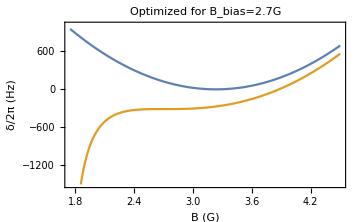

```mathematica
Ω0=2π 21.4113kHz;
Δ0=- 2π 1.15813MHz;
Clear[Δdress]
ωdress=ω0+Δdress;
params ={{0,0},{Ω0,Δ0}};
Plot[Evaluate[Array[((ΔEqubit/.{Ωdress->params[[#,1]],Δdress->params[[#,2]]})-ω0+2π 4500)/( 2π)/.B->Bdc G&,Length[params]]],{Bdc,1.75,4.5},PlotRange->{-1500,1000},FrameLabel->{"B (G)","δ/2π (Hz)"},PlotLabel->StringForm["Optimized for B_bias=``G",Boffset/G]]
```

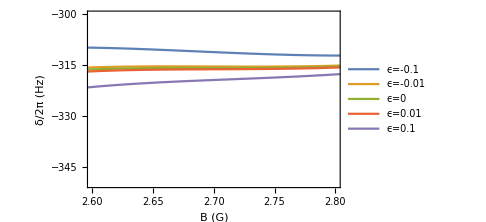

```mathematica
Ω0=2π 21.4113kHz;
Δ0=-2π 1.15813MHz;
ωdress=ω0+Δdress;
ΔEqubit=2π(E7-E3)+Ωdress^2(√(1-ϵ)c1/Δ1+√(1+ϵ)(c2/Δ2+c3/Δ3));
params={-0.1,-0.01,0,0.01,0.1};(*ϵ values*)
legend=Array[StringForm["ϵ=``",params[[#]]]&,Length[params]];
Plot[Evaluate[Array[((ΔEqubit/.{Ωdress->Ω0,Δdress->Δ0,ϵ->params[[#]]})-ω0+2π 4500)/( 2π)/.B->Bdc G&,Length[params]]],{Bdc,1.75,4.5},FrameLabel->{"B (G)","δ/2π (Hz)"},PlotRange->{{Boffset/G-0.1,Boffset/G+0.1},{-350,-300}},PlotLegends->legend]
```

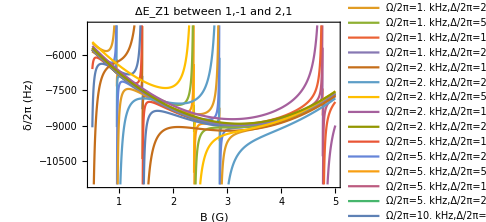

```mathematica
ΩdressTable = 2π{1,2,5,10,20}kHz;
ΔdressTable = 2π{1,2,5,10,20}MHz;
(*DressingTable = Transpose@{ΩdressTable,ΔdressTable};*)
DressingTable =Flatten[Table[{ΩdressTable[[i]],ΔdressTable[[j]]},{i,Range[Length[ΩdressTable]]},{j,Range[Length[ΔdressTable]]}],1];
Plot[Evaluate[Array[((ΔEqubit/.{Ωdress->DressingTable[[#,1]],ωdress->ω0-DressingTable[[#,2]]})-ω0-2π 4500)/( 2π)/.B->Bdc G&,Length[DressingTable]]],{Bdc,0.5,5},FrameLabel->{"B (G)","δ/2π (Hz)"},PlotLabel->"ΔE_Z1 between 1,-1 and 2,1",PlotLegends->Array[StringForm["Ω/2π=`` kHz,Δ/2π=`` MHz",Round[DressingTable[[#,1]]/(2π kHz),.01],Round[DressingTable[[#,2]]/(2π MHz),.01]]&,Length[DressingTable]]]
```

```mathematica
Flatten[Table[{ΩdressTable[[i]],ΔdressTable[[j]]},{i,Range[6]},{j,Range[6]}],1]
```

{{2000 π,2000000 π},{2000 π,4000000 π},{2000 π,10000000 π},{2000 π,20000000 π},{2000 π,40000000 π},{2000 π,100000000 π},{4000 π,2000000 π},{4000 π,4000000 π},{4000 π,10000000 π},{4000 π,20000000 π},{4000 π,40000000 π},{4000 π,100000000 π},{10000 π,2000000 π},{10000 π,4000000 π},{10000 π,10000000 π},{10000 π,20000000 π},{10000 π,40000000 π},{10000 π,100000000 π},{20000 π,2000000 π},{20000 π,4000000 π},{20000 π,10000000 π},{20000 π,20000000 π},{20000 π,40000000 π},{20000 π,100000000 π},{40000 π,2000000 π},{40000 π,4000000 π},{40000 π,10000000 π},{40000 π,20000000 π},{40000 π,40000000 π},{40000 π,100000000 π},{100000 π,2000000 π},{100000 π,4000000 π},{100000 π,10000000 π},{100000 π,20000000 π},{100000 π,40000000 π},{100000 π,100000000 π}}

### Analytical expression for magnetic decoherence

```mathematica
ω0=2π 6.8346826109 GHz;(*I defined EHF to more precision than they do.(EHF/h)*);
Δdress=ωdress-ω0;
μ1=2π*702.37kHz/G;
μ2=2π*699.58kHz/G;
β=2π*71.89/G^2;
ΔEqubit=ω0+(μ2-μ1)B+6β B^2
```

4.29436×10^10-1.75301×10^8 B+2.71019×10^11 B^2

### Effect of magnetic fluctuations on coherence in the presence of microwave dressing

Compute estimated coherence assuming slow magnetic noise (2π f_noise<<Ω_dress,Δ_dress).

```mathematica
(*Average a Ramsey measurement in which the qubit sees a phase shift ϕ=bt, where b is a frequency shift sampled from a Gaussian distribution*)
Assuming[σ∈Reals&&σ>0,Integrate[Cos[b t] 1/(√(2π)σ)Exp[-b^2/(2 σ^2)],{b,-∞,∞}]]
```

ⅇ^(-1/2 t^2 σ^2)

```mathematica
T2star=√2/σ;
```

The standard deviation of the frequency shift, σ, depends on the standard deviation of environmental magnetic field fluctuations (e.g. from the stability of the coil driver current) through the differential Zeeman shift on the qubit transition.

```mathematica
σB=0.01G;
Bdist=1/(√(2π)σB)Exp[(-(B-Boffset)^2)/(2 σB^2)];
```

```mathematica
(*compute the std from a fininte sample*)
Clear[ΔE];
Boffset=3.23G;
Ω0=Δ0=0;
ΔE[B_]=ΔEqubit/.{Ωdress->Ω0,Δdress->Δ0,ϵ->0};(*units of angular frequency*)
"σΔE (Hz)"
σΔE=StandardDeviation[Map[ΔE,RandomVariate[NormalDistribution[Boffset,σB],100000]]]
StringForm["T2^*=`` s, B_bias=`` G, Ω_dress/2π=`` kHz, Δ_dress/2π=`` MHz, σ_B=`` G", (√2)/σΔE,Boffset/G,Ω0/(2π kHz),Δ0/(2π MHz),σB/G]
```

σΔE (Hz)

0.471268

T2^*=3.00087 s, B_bias=3.23 G, Ω_dress/2π=0 kHz, Δ_dress/2π=0 MHz, σ_B=0.01 G

```mathematica
Clear[ΔE];
Boffset=2.7G;
Ω0=2π 21.4113kHz;
Δ0=-2π 1.15813MHz;
ΔE[B_]=ΔEqubit/.{Ωdress->Ω0,Δdress->Δ0,ϵ->0};(*units of angular frequency*)
"σΔE (Hz)"
σΔE=StandardDeviation[Map[ΔE,RandomVariate[NormalDistribution[Boffset,σB],100000]]]
StringForm["T2^*=`` s, B_bias=`` G, Ω_dress/2π=`` kHz, Δ_dress/2π=`` MHz, σ_B=`` G", (√2)/σΔE,Boffset/G,Ω0/(2π kHz),Δ0/(2π MHz),σB/G]
```

σΔE (Hz)

10.7867

T2^*=0.131107 s, B_bias=2.7 G, Ω_dress/2π=21.4113 kHz, Δ_dress/2π=-1.15813 MHz, σ_B=0.1 G

```mathematica
T2starTable={};
σBTable={0.1,0.05,0.01,0.005,0.001}G;
Boffset=2.7G ;
Ω0=2π 21.4113kHz;
Δ0=- 2π 1.15813MHz;
(*Boffset=3.23G;
Ω0=Δ0=0;*)
For[i=1,i<Length[σBTable]+1,i++,
σB=σBTable[[i]];
Clear[ΔE];
ΔE[B_]=ΔEqubit/.{Ωdress->Ω0,Δdress->Δ0,ϵ->0};(*units of angular frequency*)
"σΔE (Hz)";
σΔE=StandardDeviation[Map[ΔE,RandomVariate[NormalDistribution[Boffset,σB],100000]]];
StringForm["T2^*=`` s, B_bias=`` G, Ω_dress/2π=`` kHz, Δ_dress/2π=`` MHz, σ_B=`` G", (√2)/σΔE,Boffset/G,Ω0/(2π kHz),Δ0/(2π MHz),σB/G];
AppendTo[T2starTable,(√2)/σΔE];
]
```

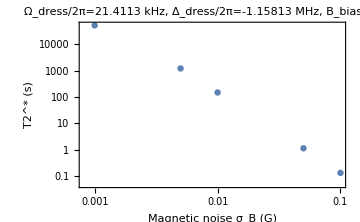

```mathematica
ListLogLogPlot[Transpose@{σBTable/G,T2starTable},FrameLabel->{"Magnetic noise σ_B (G)","T2^* (s)"},PlotLabel->Style[StringForm["Ω_dress/2π=`` kHz, Δ_dress/2π=`` MHz, \nB_bias=`` G", Ω0/(2π kHz),Δ0/(2π MHz),Boffset/G],FontSize->14]]
```

```mathematica
T2starTable={};
σBTable={0.1,0.05,0.01,0.005,0.001}G;
Boffset=3.23G;
Ω0=Δ0=0;
For[i=1,i<Length[σBTable]+1,i++,
σB=σBTable[[i]];
Clear[ΔE];
ΔE[B_]=ΔEqubit/.{Ωdress->Ω0,Δdress->Δ0,ϵ->0};(*units of angular frequency*)
"σΔE (Hz)";
σΔE=StandardDeviation[Map[ΔE,RandomVariate[NormalDistribution[Boffset,σB],100000]]];
StringForm["T2^*=`` s, B_bias=`` G, Ω_dress/2π=`` kHz, Δ_dress/2π=`` MHz, σ_B=`` G", (√2)/σΔE,Boffset/G,Ω0/(2π kHz),Δ0/(2π MHz),σB/G];
AppendTo[T2starTable,(√2)/σΔE];
]
```

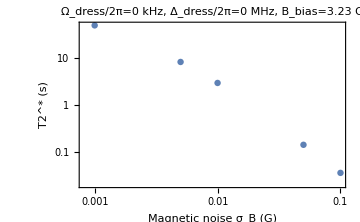

```mathematica
ListLogLogPlot[Transpose@{σBTable/G,T2starTable},FrameLabel->{"Magnetic noise σ_B (G)","T2^* (s)"},PlotLabel->Style[StringForm["Ω_dress/2π=`` kHz, Δ_dress/2π=`` MHz, \nB_bias=`` G", Ω0/(2π kHz),Δ0/(2π MHz),Boffset/G],FontSize->14]]
```

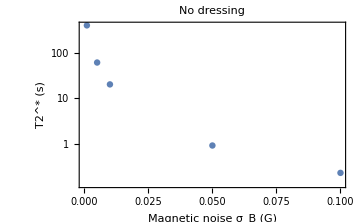

```mathematica
ListLogPlot[Transpose@{σBTable/G,T2starTable},FrameLabel->{"Magnetic noise σ_B (G)","T2^* (s)"},PlotLabel->"No dressing"]
```

### Solve by diagonalizing the full AC + DC Zeeman Hamiltonian

Probably not necessary but a good excercise.

```mathematica
Inuc=3/2;
S = 1/2; 
L = 0; 
J = 1/2;
gJ=gL(J(J+1)+L(L+1)-S(S+1)
+gS(J(J+1)-L(L+1)+S(S+1)))/(2J(J+1));
gF = (gJ(F(F+1)+J(J+1)-Inuc(Inuc+1))
+gI(F(F+1)-J(J+1)+Inuc(Inuc+1)))/(2F(F+1));
F= 1;FF=2;
(*The leading factor of 1/√2 is the amplitude Bσ_±Subscript[Bπ, x]*)
mF =-1;mFF=-2;
"2,-2H1,-1/(ℏ μB gF)"
c1 =1/(√2)ClebschGordan[{F,mF},{1,mFF-mF},{FF,mFF}] √(2 F +1)(-1)^(1+J+Inuc)(gJ (-1)^F √(J (J+1)(2 J+1))SixJSymbol[{J,Inuc,F},{FF,1,J}]+
gI(-1)^FF √(Inuc(Inuc+1)(2Inuc+1))SixJSymbol[{Inuc,J,F},{FF,1,Inuc}])/gF
(*2,-2H1,-1/(ℏ μB gF)*)
mF =-1;mFF=0;
"2,0H1,-1/(ℏ μB gF)"
c2= 1/(√2) ClebschGordan[{F,mF},{1,mFF-mF},{FF,mFF}] √(2 F +1)(-1)^(1+J+Inuc)(gJ (-1)^F √(J (J+1)(2 J+1))SixJSymbol[{J,Inuc,F},{FF,1,J}]+
gI(-1)^FF √(Inuc(Inuc+1)(2Inuc+1))SixJSymbol[{Inuc,J,F},{FF,1,Inuc}])/gF(*2,0H1,-1/(ℏ μB gF)*)
mF =0;mFF=1;
"2,1H1,0/(ℏ μB gF)"
c3=1/(√2) ClebschGordan[{F,mF},{1,mFF-mF},{FF,mFF}] √(2 F +1)(-1)^(1+J+Inuc)(gJ (-1)^F √(J (J+1)(2 J+1))SixJSymbol[{J,Inuc,F},{FF,1,J}]+
gI(-1)^FF √(Inuc(Inuc+1)(2Inuc+1))SixJSymbol[{Inuc,J,F},{FF,1,Inuc}])/gF(*2,1H1,0/(ℏ μB gF)*)
```

2,-2H1,-1/(ℏ μB gF)

-1.72861

2,0H1,-1/(ℏ μB gF)

-0.705703

2,1H1,0/(ℏ μB gF)

-1.22231

```mathematica
(*double letter labels for the upper state quantum numbers*)
HFZ1MatElem[I_,J_,gJ_,{F_,mF_},{FF_,mFF_},Bz_]:=Quiet[μB Bz (ClebschGordan[{F,mF},{1,0},{FF,mFF}] √(2 F +1)(-1)^(1+J+I)(gJ (-1)^F √(J (J+1)(2 J+1))SixJSymbol[{J,I,F},{FF,1,J}]+
gI(-1)^FF √(I(I+1)(2I+1))SixJSymbol[{I,J,F},{FF,1,I}]))];
KetForm[{F_,m_}]:=F,m;(*for printing nice labels*)
states = Flatten[Table[Table[{F,mF},{mF,-F,F}],{F,{2,1}}],1];
states=Join[states[[1;;4]],states[[6;;]]];(*we don't need the 2,2 state*)
"basis"
Array[KetForm[states[[#]]]&,7]
dim = Length[states];
HZ1[Bz_]=Table[Table[JToeV[HFZ1MatElem[Inuc,J,gJ,states[[i]],states[[j]],Bz]],{i,1,dim}],{j,1,dim}];
Clear[ΩeV,ΔeV];
Hdress=({{ΔeV, 0, 0, 0, c1 ΩeV, 0, 0}, {0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, c2 ΩeV, 0, 0}, {0, 0, 0, 0, 0, c3 ΩeV, 0}, {c1 ΩeV, 0, c2 ΩeV, 0, ΔeV, 0, 0}, {0, 0, 0, c3 ΩeV, 0, ΔeV, 0}, {0, 0, 0, 0, 0, 0, 0}});(*the AC dressing... not sure if this is the correct way of taking the frequency into account*)
HAtom = Array[0&,{dim,dim}];
Array[(HAtom[[#,#]]=EHFeV)&,4];
Hdc=HAtom + HZ1[B];
Energies=10^9 eVToGHz[SortBy[Assuming[ΩeV∈Reals&&ΔeV∈Reals&&ΩeV>0,Eigenvalues[Hdc,Method->"Direct"]],#/.{B->0.1,ΩeV->0,ΔeV->0}&]];
(*Eigenenergies in Hz*)
```

basis

{2,-2,2,-1,2,0,2,1,1,-1,1,0,1,1}

todo: take reproduce the plot with the cancelled differential shift using the energies from the diagonalized system above

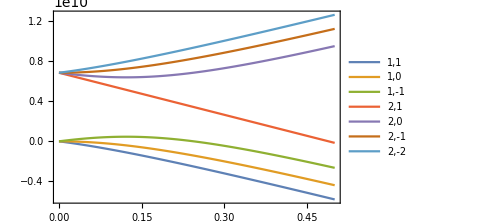

```mathematica
Plot[Evaluate[Array[Energies[[#]]/.{ΩeV->0,ΔeV->0}&,dim]],{B,0,0.5},PlotLegends->Reverse[Array[KetForm[states[[#]]]&,dim]]]
```

Numerically evaluate the eigenvalues for definite values of dc and ac field.

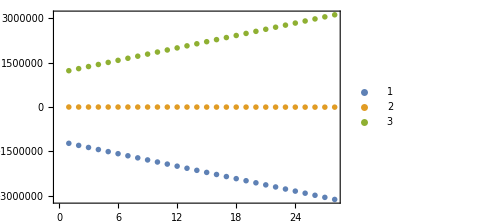

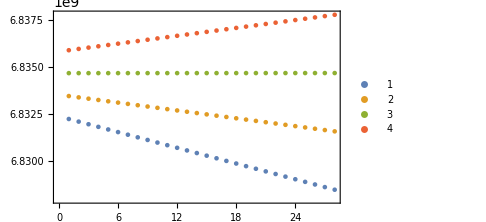

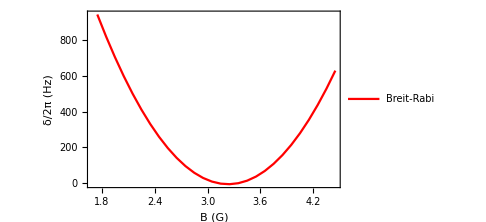

```mathematica
ΩeV=ΔeV=0;
Blist=Range[1.75,4.5,0.1];
eigenvalTable=Transpose@Table[10^9 eVToGHz[Sort[Eigenvalues[Hdc/.{B->Bdc G}]]],{Bdc,Blist}];
ListPlot[Evaluate[eigenvalTable[[;;3]]],PlotLegends->Automatic]
ListPlot[Evaluate[eigenvalTable[[4;;]]],PlotLegends->Automatic]
BreitRabi=ListPlot[Transpose@{Blist,eigenvalTable[[7]]-eigenvalTable[[3]]-EHF/h+4500},Joined->True,FrameLabel->{"B (G)","δ/2π (Hz)"},PlotLegends->{"Breit-Rabi"},PlotStyle->Red]
```

```mathematica
"states:"
Reverse[Array[{8-#,KetForm[states[[#]]]}&,dim]]
```

states:

{{1,1,1},{2,1,0},{3,1,-1},{4,2,1},{5,2,0},{6,2,-1},{7,2,-2}}

```mathematica
(*add the AC dressing Hamiltonian and diagonalize*)
Clear[E4,E6,E7,E3,E6]
ΔEshifts={};
ω0=2π EHF/h;
For[i=1,i<Length[Blist]+1,i++,
dcShifts=10^9 eVToGHz[Sort[Eigenvalues[Hdc/.{B->Blist[[i]] G}]]];
E4=GHz eVToGHz[Series[dcShifts[[4]],{B,0,2}]]//Normal;(*"2,-2"*)
E6=GHz eVToGHz[Series[dcShifts[[6]],{B,0,2}]]//Normal;(*"2,0"*)
E2=GHz eVToGHz[Series[dcShifts[[2]],{B,0,2}]]//Normal;(*"1,0"*)
E3=GHz eVToGHz[Series[dcShifts[[3]],{B,0,2}]]//Normal;(*"1,-1" 0*)
E7=GHz eVToGHz[Series[dcShifts[[7]],{B,0,2}]]//Normal;(*"2,1 1"*)
Δdress= ωdress-ω0;
ω0=2π(E7-E3)/.B->Blist[[i]]G;
Δ1=(Δdress+2π( E3-E4)+ω0)/.B->Blist[[i]]G;
Δ2=(Δdress+2π(E3-E6)+ω0)/.B->Blist[[i]]G;
Δ3=(Δdress+2π(E2-E7)+ω0)/.B->Blist[[i]]G;
(*basis includes states 2,3,4,6,7, ordered from lowest to highest in the dc-shifted basis*)
Ω1=c1 Ωdress;
Ω2=c2 Ωdress;
Ω3=c3 Ωdress;
Hrwa=({{0, 0, 0, 0, Ω3}, {0, 0, Ω1, Ω2, 0}, {0, Ω1, Δ1, 0, 0}, {0, Ω2, 0, Δ2, 0}, {Ω3, 0, 0, 0, Δ3}});(*the RWA hamiltonian including dressing-- this isn't correct*)
dressedEnergies=SortBy[Assuming[Ωdress∈Reals&&ωdress∈Reals&&ωdress>0,Eigenvalues[Hrwa]],#/.{Ωdress->0,ωdress->0}&];
AppendTo[ΔEshifts,dressedEnergies[[5]]-dressedEnergies[[2]]];
]
```

```mathematica
(*Ω0=2π 21.4113kHz;
Δ0=- 2π 1.15813MHz;*)
Ω0=0;
Δ0=0;
ListPlot[Transpose@{Blist,ΔEshifts/.{ωdress->ω0+Δ0, Ωdress->Ω0}}]
```

-Graphics-

```mathematica
Clear[Ω1,Ω2,Ω3,Δ1,Δ2,Δ3]
```

```mathematica
Hrwa=({{0, 0, 0, 0, Ω3}, {0, 0, Ω1, Ω2, 0}, {0, Ω1, Δ1, 0, 0}, {0, Ω2, 0, Δ2, 0}, {Ω3, 0, 0, 0, Δ3}});
Assuming[Ω1∈Reals&&Δ1∈Reals&&Ω2∈Reals&&Δ2∈Reals&&Ω3∈Reals&&Δ3∈Reals,Eigenvalues[Hrwa]]
```

{1/2 (Δ3-√(Δ3^2+4 Ω3^2)),1/2 (Δ3+√(Δ3^2+4 Ω3^2)),Root[Δ2 Ω1^2+Δ1 Ω2^2+(Δ1 Δ2-Ω1^2-Ω2^2) #1+(-Δ1-Δ2) #1^2+#1^3&,1],Root[Δ2 Ω1^2+Δ1 Ω2^2+(Δ1 Δ2-Ω1^2-Ω2^2) #1+(-Δ1-Δ2) #1^2+#1^3&,2],Root[Δ2 Ω1^2+Δ1 Ω2^2+(Δ1 Δ2-Ω1^2-Ω2^2) #1+(-Δ1-Δ2) #1^2+#1^3&,3]}

```mathematica
Length[Blist]
```

28

```mathematica
Length[ΔEshifts]
```

27

```mathematica
HdcDiagnolized/.Bdc->3.23
```

{{6.83017×10^9,0,0,0,0,0,0},{0,2.26412×10^6,0,0,0,0,0},{0,0,6.83243×10^9,0,0,0,0},{0,0,0,-6.83695×10^9,0,0,0},{0,0,0,0,2.25962×10^6,0,0},{0,0,0,0,0,-6.83469×10^9,0},{0,0,0,0,0,0,2994.18}}

```mathematica
x={1,2,4,8};
Array[x[[#+1]]&,3]
```

{2,4,8}

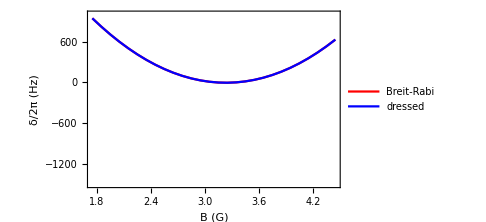

-Graphics-

-Graphics-

-Graphics-

-Graphics-

```mathematica
blist={0.1,0.5,1,1.5,10};
For[i=0,i<Length[blist],i++,
b=blist[[i]];
ΩeV= b 2π 21.4113 kHz 10^-19;
ΔeV=-b 2π 1.15813MHz 10^-19;
Blist=Range[1.75,4.5,0.1];
eigenvalTable=Transpose@Table[10^9 eVToGHz[Sort[Eigenvalues[Hdc/.{B->Bdc G}]]],{Bdc,Blist}];
Print[Show[BreitRabi,ListPlot[Transpose@{Blist,eigenvalTable[[7]]-eigenvalTable[[3]]-EHF/h+4500},Joined->True,FrameLabel->{"B (G)","δ/2π (Hz)"},PlotStyle->Blue,PlotLegends->{"dressed"}],PlotRange->{-1500,1000}]]
]
```

```mathematica
GHzToeV[1]/GHz
```

4.13567×10^-15

Try to solve for the dressing parameters by not evaluating the eigenvalues right away.

```mathematica
Clear[ΩeV,ΔeV];
Boffset=2.7G;
{Δdress,Ωsoln}=Transpose@Chop[Values[NSolve[{(D[,B]/.B->Boffset)==0,(D[ΔEqubit,{B,2}]/.B->Boffset)==0},{Ωdress,Δdress},Reals]]];
Join[{{"Ωdress/2π (MHz)","Δdress/2π (kHz)"}},Transpose@{Ωsoln/(2π kHz),Δdress/(2π MHz)}]//TableForm
```

```mathematica
ΔEqubit/.{B->2.7G,Ω1eV->0,Ω2eV->0,Ω3eV->0,ΔeV->0}
```

-2.83412×10^6

```mathematica
Clear[Ω1eV,Ω2eV,Ω3eV,ΔeV,Δdress];
(*Ω1eV=GHzToeV[10^-9 c1 μB gF Ωdress];
Ω2eV=GHzToeV[10^-9 c2 μB gF Ωdress];
Ω3eV=GHzToeV[10^-9 c3 μB gF Ωdress];
 ΔeV=GHzToeV[10^-9 Δdress];*)
(*Ω1eV=c1 Ωdress;
Ω2eV=c2 Ωdress;
Ω3eV=c3 Ωdress;
Δdress=ΔeV;*)
Boffset=2.7G;
{Δdress,Ωsoln}=Transpose@Chop[Values[NSolve[{(D[,B]/.B->Boffset)==0,(D[ΔEqubit,{B,2}]/.B->Boffset)==0},{Ωdress,Δdress},Reals]]];
Join[{{"Ωdress/2π (MHz)","Δdress/2π (kHz)"}},Transpose@{Ωsoln/(2π kHz),Δdress/(2π MHz)}]//TableForm
```

Set::shape: Lists {Δdress,Ωsoln} and {} are not the same shape.

Ωdress/2π (MHz) | Δdress/2π (kHz)
Ωsoln/(2000 π) | 
Δdress/(2000000 π) |

### Analysis for the case of dressing states which are not near a magic condition

#### |1,-1> and |1,1>, which will be relevant for our network

The analysis below is fruitless, but copy the 2,-2 to 2,2 cell below and use the same approach to find a solution.

```mathematica
Inuc=3/2;
S = 1/2; 
L = 0; 
J = 1/2;
gJ=gL(J(J+1)+L(L+1)-S(S+1)
+gS(J(J+1)-L(L+1)+S(S+1)))/(2J(J+1));
gF = (gJ(F(F+1)+J(J+1)-Inuc(Inuc+1))
+gI(F(F+1)-J(J+1)+Inuc(Inuc+1)))/(2F(F+1));
F= 1;FF=2;
(*The leading factor of 1/√2 is the amplitude Bσ_±Subscript[Bπ, x]*)
mF =-1;mFF=-1;
"2,-1H1,-1/(ℏ μB gF)"
c1 =ClebschGordan[{F,mF},{1,mFF-mF},{FF,mFF}] √(2 F +1)(-1)^(1+J+Inuc)(gJ (-1)^F √(J (J+1)(2 J+1))SixJSymbol[{J,Inuc,F},{FF,1,J}]+
gI(-1)^FF √(Inuc(Inuc+1)(2Inuc+1))SixJSymbol[{Inuc,J,F},{FF,1,Inuc}])/gF
(*2,-2H1,-1/(ℏ μB gF)*)
mF =1;mFF=1;
"2,1H1,1/(ℏ μB gF)"
c2=  ClebschGordan[{F,mF},{1,mFF-mF},{FF,mFF}] √(2 F +1)(-1)^(1+J+Inuc)(gJ (-1)^F √(J (J+1)(2 J+1))SixJSymbol[{J,Inuc,F},{FF,1,J}]+
gI(-1)^FF √(Inuc(Inuc+1)(2Inuc+1))SixJSymbol[{Inuc,J,F},{FF,1,Inuc}])/gF(*2,0H1,-1/(ℏ μB gF)*)
```

2,-1H1,-1/(ℏ μB gF)

-1.72861

2,1H1,1/(ℏ μB gF)

-1.72861

```mathematica
Clear[ωdress,Δdress,Ωdress,Ωsoln,Δsoln]
E4=GHz eVToGHz[Series[ZShifts[B][[4]],{B,0,2}]]//Normal(*"2,-2"*)
E5=GHz eVToGHz[Series[ZShifts[B][[5]],{B,0,2}]]//Normal(*"2,-1"*)
E6=GHz eVToGHz[Series[ZShifts[B][[6]],{B,0,2}]]//Normal(*"2,0"*)
E1=GHz eVToGHz[Series[ZShifts[B][[1]],{B,0,2}]]//Normal(*"1,1"*)
E2=GHz eVToGHz[Series[ZShifts[B][[2]],{B,0,2}]]//Normal(*"1,0"*)
E3=GHz eVToGHz[Series[ZShifts[B][[3]],{B,0,2}]]//Normal(*"1,-1" 0*)
E7=GHz eVToGHz[Series[ZShifts[B][[7]],{B,0,2}]]//Normal(*"2,1 1"*)
ω0=2π(E7-E3)/.B->0;
Δ1=Δdress+2π(E3-E5)+ω0;
Δ2=Δdress+2π(E1-E7)+ω0;
ΔEqubit=2π(E3-E1)+Ωdress^2(c1/Δ1+c2/Δ2);
Boffset=0G;
{Δsoln,Ωsoln}=Transpose@Chop[Values[NSolve[{(D[ΔEqubit,B]/.B->Boffset)==0,(D[ΔEqubit,{B,2}]/.B->Boffset)==0},{Δdress,Ωdress},Reals]]];
(*DressingTable=Select[Transpose@{Ωsoln,Δsoln},(#[[1]]>0&&#[[1]]<2π 100 kHz)&];*)
(*Join[{{"Ωdress/2π (kHz)","Δdress/2π (MHz)"}},Select[Transpose@{Ωsoln/(2π kHz),Δsoln/(2π MHz)},(#[[1]]>0)&]]//TableForm*)
DressingTable=Transpose@{Ωsoln,Δsoln};
Join[{{"Ωdress/2π (kHz)","Δdress/2π (MHz)"}},Transpose@{Ωsoln/(2π kHz),Δsoln/(2π MHz)}]//TableForm
```

6.83468×10^9-1.39776×10^10 B

6.83468×10^9-6.98878×10^9 B+2.15246×10^10 B^2

6.83468×10^9+2.86994×10^10 B^2

-7.01663×10^9 B-2.15246×10^10 B^2

-2.86994×10^10 B^2

7.01663×10^9 B-2.15246×10^10 B^2

6.83468×10^9+6.98878×10^9 B+2.15246×10^10 B^2

Set::shape: Lists {Δsoln,Ωsoln} and {} are not the same shape.

Ωdress/2π (kHz) | Δdress/2π (MHz)
Ωsoln/(2000 π) | 
Δsoln/(2000000 π) |

```mathematica
{Ωsoln,Δsoln}
```

{{-3.27622×10^11},{0}}

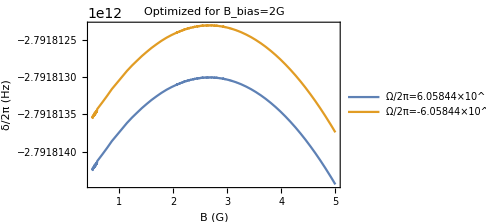

```mathematica
Plot[Evaluate[Array[((ΔEqubit/.{Ωdress->DressingTable[[#,1]],Δdress->DressingTable[[#,2]]})-ω0+2π 4500)/( 2π)/.B->Bdc G&,Length[DressingTable]]],{Bdc,0.5,5},FrameLabel->{"B (G)","δ/2π (Hz)"},PlotLabel->StringForm["Optimized for B_bias=``G",Boffset/G,θ],PlotLegends->Array[StringForm["Ω/2π=`` kHz,Δ/2π=`` MHz",Round[DressingTable[[#,1]]/(2π kHz),.01],Round[DressingTable[[#,2]]/(2π MHz),.01]]&,Length[DressingTable]]]
```

```mathematica
D
```

```mathematica
BoffsetTable={2.5,2.75,3}G;
linesTable={};
legendsTable={};
For[i=1,i<Length[BoffsetTable]+1,i++,
Boffset=BoffsetTable[[i]];
{Δsoln,Ωsoln}=Transpose@Chop[Values[NSolve[{(D[ΔEqubit,B]/.B->Boffset)==0,(D[ΔEqubit,{B,2}]/.B->Boffset)==0},{Δdress,Ωdress},Reals]]];
DressingTable=Select[Transpose@{Ωsoln,Δsoln},(#[[1]]>0&&#[[1]]<2π 100 kHz)&];
AppendTo[linesTable,Evaluate[Array[((ΔEqubit/.{Ωdress->DressingTable[[#,1]],Δdress->DressingTable[[#,2]]})-ω0+2π 4500)/( 2π)/.B->Bdc G&,Length[DressingTable]]]];
AppendTo[legendsTable,Array[StringForm["Ω/2π=`` kHz,Δ/2π=`` MHz",Round[DressingTable[[#,1]]/(2π kHz),.01],Round[DressingTable[[#,2]]/(2π MHz),.01]]&,Length[DressingTable]]];
];
lines=Join[{((ΔEqubit-ω0+2π 4500)/( 2π)/.{B->Bdc G,Ωdress->0,Δdress->0})},Flatten@linesTable];
legends=Join[{StringForm["Ω/2π=`` kHz,Δ/2π=`` MHz",0,0]},Flatten@legendsTable];
Plot[lines,{Bdc,1.75,4.5},PlotRange->{-1500,1000},FrameLabel->{"B (G)","δ/2π (Hz)"},PlotLabel->StringForm["ΔE_((1, -1), (1, 1))",Boffset/G],PlotLegends->legends]
```

-Graphics-

#### |2,-2> and |2,2>, which are relevant for Omar’s scheme

dress with linearly polarized light perpendicular to the quantization axis, such that we couple to σ transitions.  the numerical solver doesn’t find the solution, but scroll down to where I plot the differential shift vs B for several dressing parameters. a solution can be found for the first derivative to go to zero if the bias field and either detuning or Rabi frequency are fixed.

```mathematica
Inuc=3/2;
S = 1/2; 
L = 0; 
J = 1/2;
gJ=gL(J(J+1)+L(L+1)-S(S+1)
+gS(J(J+1)-L(L+1)+S(S+1)))/(2J(J+1));
gF = (gJ(F(F+1)+J(J+1)-Inuc(Inuc+1))
+gI(F(F+1)-J(J+1)+Inuc(Inuc+1)))/(2F(F+1));
F= 1;FF=2;
(*The leading factor of 1/√2 is the amplitude Bσ_±Subscript[Bπ, x]*)
mF =-1;mFF=-2;
c1 =ClebschGordan[{F,mF},{1,mFF-mF},{FF,mFF}] √(2 F +1)(-1)^(1+J+Inuc)(gJ (-1)^F √(J (J+1)(2 J+1))SixJSymbol[{J,Inuc,F},{FF,1,J}]+
gI(-1)^FF √(Inuc(Inuc+1)(2Inuc+1))SixJSymbol[{Inuc,J,F},{FF,1,Inuc}])/gF
(*2,-2H1,-1/(ℏ μB gF)*)
mF =1;mFF=2;
c2=  ClebschGordan[{F,mF},{1,mFF-mF},{FF,mFF}] √(2 F +1)(-1)^(1+J+Inuc)(gJ (-1)^F √(J (J+1)(2 J+1))SixJSymbol[{J,Inuc,F},{FF,1,J}]+
gI(-1)^FF √(Inuc(Inuc+1)(2Inuc+1))SixJSymbol[{Inuc,J,F},{FF,1,Inuc}])/gF(*2,0H1,-1/(ℏ μB gF)*)

Clear[ωdress,Δdress,Ωdress,Ωsoln,Δsoln]
(*the state energies numbered in order from lowest energy (1,1) to highest (2,2)*)
(*E4=GHz eVToGHz[Series[ZShifts[B][[4]],{B,0,2}]]//Normal(*"2,-2"  0*);
E5=GHz eVToGHz[Series[ZShifts[B][[5]],{B,0,2}]]//Normal(*"2,-1"*);
E6=GHz eVToGHz[Series[ZShifts[B][[6]],{B,0,2}]]//Normal(*"2,0"*);
E1=GHz eVToGHz[Series[ZShifts[B][[1]],{B,0,2}]]//Normal(*"1,1"*);
E2=GHz eVToGHz[Series[ZShifts[B][[2]],{B,0,2}]]//Normal(*"1,0"*);
E3=GHz eVToGHz[Series[ZShifts[B][[3]],{B,0,2}]]//Normal(*"1,-1"*);
E7=GHz eVToGHz[Series[ZShifts[B][[7]],{B,0,2}]]//Normal(*"2,1"*);
E8=GHz eVToGHz[Series[ZShifts[B][[8]],{B,0,2}]]//Normal(*"2,2" 1*);
ω0=2π(E7-E3)/.B->0;
Δ1=Δdress+2π(E3-E4)+ω0;
Δ2=Δdress+2π(E1-E8)+ω0;
ΔEqubit=2π(E4-E8)+Ωdress^2(c1^2/Δ1+c2^2/Δ2);*)

Clear[ωdress,Δdress,Ωdress,Ωsoln,Δsoln]
(*the state energies numbered in order from lowest energy (1,1) to highest (2,2)*)
E4=GHz eVToGHz[Series[ZShifts[B][[4]],{B,0,1}]]//Normal(*"2,-2"  0*)
E5=GHz eVToGHz[Series[ZShifts[B][[5]],{B,0,1}]]//Normal(*"2,-1"*)
E6=GHz eVToGHz[Series[ZShifts[B][[6]],{B,0,1}]]//Normal(*"2,0"*)
E1=GHz eVToGHz[Series[ZShifts[B][[1]],{B,0,1}]]//Normal(*"1,1"*)
E2=GHz eVToGHz[Series[ZShifts[B][[2]],{B,0,1}]]//Normal(*"1,0"*)
E3=GHz eVToGHz[Series[ZShifts[B][[3]],{B,0,1}]]//Normal(*"1,-1"*)
E7=GHz eVToGHz[Series[ZShifts[B][[7]],{B,0,1}]]//Normal(*"2,1"*)
E8=GHz eVToGHz[Series[ZShifts[B][[8]],{B,0,1}]]//Normal(*"2,2" 1*)
ω0=2π(E7-E3)/.B->0;
Δ1=Δdress+2π(E3-E4)+ω0;
Δ2=Δdress+2π(E1-E8)+ω0;
ΔEqubit=2π(E4-E8)+Ωdress^2(c1^2/Δ1+c2^2/Δ2);
```

-2.44463

-2.44463

6.83468×10^9-1.39776×10^10 B

6.83468×10^9-6.98878×10^9 B

6.83468×10^9

-7.01663×10^9 B

0

7.01663×10^9 B

6.83468×10^9+6.98878×10^9 B

6.83468×10^9+1.39776×10^10 B

```mathematica
Blist = Range[0,1,0.05];
For[i=1,i<Length[Blist],i++,
Boffset=Blist[[i]]G;
{Δsoln,Ωsoln}=Transpose@Chop[Values[NSolve[{(D[ΔEqubit,B]/.B->Boffset)==0,(D[ΔEqubit,{B,2}]/.B->Boffset)==0},{Δdress,Ωdress},Reals]]];
Print["Boffset=",Boffset/G];
Print[DressingTable=Transpose@{Ωsoln,Δsoln};
Join[{{"Ωdress/2π (kHz)","Δdress/2π (MHz)"}},Transpose@{Ωsoln/(2π kHz),Δsoln/(2π MHz)}]//TableForm];
]

(*Clear[Boffset];
Transpose@Chop[Values[NSolve[{(D[ΔEqubit,B])==0,(D[ΔEqubit,{B,2}])==0},{Δdress,Ωdress,B},Reals]]]*)
```

Set::shape: Lists {Δsoln,Ωsoln} and {} are not the same shape.

Boffset=0.

Ωdress/2π (kHz) | Δdress/2π (MHz)
Ωsoln/(2000 π) | 
Δsoln/(2000000 π) |

Set::shape: Lists {Δsoln,Ωsoln} and {} are not the same shape.

Boffset=0.05

Ωdress/2π (kHz) | Δdress/2π (MHz)
Ωsoln/(2000 π) | 
Δsoln/(2000000 π) |

Set::shape: Lists {Δsoln,Ωsoln} and {} are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Boffset=0.1

Ωdress/2π (kHz) | Δdress/2π (MHz)
Ωsoln/(2000 π) | 
Δsoln/(2000000 π) |

Boffset=0.15

Ωdress/2π (kHz) | Δdress/2π (MHz)
Ωsoln/(2000 π) | 
Δsoln/(2000000 π) |

Boffset=0.2

Ωdress/2π (kHz) | Δdress/2π (MHz)
Ωsoln/(2000 π) | 
Δsoln/(2000000 π) |

Boffset=0.25

Ωdress/2π (kHz) | Δdress/2π (MHz)
Ωsoln/(2000 π) | 
Δsoln/(2000000 π) |

Boffset=0.3

Ωdress/2π (kHz) | Δdress/2π (MHz)
Ωsoln/(2000 π) | 
Δsoln/(2000000 π) |

Boffset=0.35

Ωdress/2π (kHz) | Δdress/2π (MHz)
Ωsoln/(2000 π) | 
Δsoln/(2000000 π) |

Boffset=0.4

Ωdress/2π (kHz) | Δdress/2π (MHz)
Ωsoln/(2000 π) | 
Δsoln/(2000000 π) |

Boffset=0.45

Ωdress/2π (kHz) | Δdress/2π (MHz)
Ωsoln/(2000 π) | 
Δsoln/(2000000 π) |

Boffset=0.5

Ωdress/2π (kHz) | Δdress/2π (MHz)
Ωsoln/(2000 π) | 
Δsoln/(2000000 π) |

Boffset=0.55

Ωdress/2π (kHz) | Δdress/2π (MHz)
Ωsoln/(2000 π) | 
Δsoln/(2000000 π) |

Boffset=0.6

Ωdress/2π (kHz) | Δdress/2π (MHz)
Ωsoln/(2000 π) | 
Δsoln/(2000000 π) |

Boffset=0.65

Ωdress/2π (kHz) | Δdress/2π (MHz)
Ωsoln/(2000 π) | 
Δsoln/(2000000 π) |

Boffset=0.7

Ωdress/2π (kHz) | Δdress/2π (MHz)
Ωsoln/(2000 π) | 
Δsoln/(2000000 π) |

Boffset=0.75

Ωdress/2π (kHz) | Δdress/2π (MHz)
Ωsoln/(2000 π) | 
Δsoln/(2000000 π) |

Boffset=0.8

Ωdress/2π (kHz) | Δdress/2π (MHz)
Ωsoln/(2000 π) | 
Δsoln/(2000000 π) |

Boffset=0.85

Ωdress/2π (kHz) | Δdress/2π (MHz)
Ωsoln/(2000 π) | 
Δsoln/(2000000 π) |

Boffset=0.9

Ωdress/2π (kHz) | Δdress/2π (MHz)
Ωsoln/(2000 π) | 
Δsoln/(2000000 π) |

Boffset=0.95

Ωdress/2π (kHz) | Δdress/2π (MHz)
Ωsoln/(2000 π) | 
Δsoln/(2000000 π) |

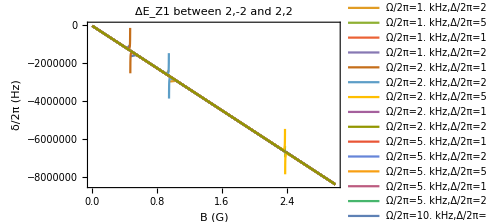

```mathematica
ΩdressTable = 2π{1,2,5,10,20}kHz;
ΔdressTable = 2π{1,2,5,10,20}MHz;
(*DressingTable = Transpose@{ΩdressTable,ΔdressTable};*)
DressingTable =Flatten[Table[{ΩdressTable[[i]],ΔdressTable[[j]]},{i,Range[Length[ΩdressTable]]},{j,Range[Length[ΔdressTable]]}],1];
Plot[Evaluate[Array[((ΔEqubit/.{Ωdress->DressingTable[[#,1]],Δdress->DressingTable[[#,2]]}))/( 2π)/.B->Bdc G&,Length[DressingTable]]],{Bdc,0.01,3},FrameLabel->{"B (G)","δ/2π (Hz)"},PlotLabel->"ΔE_Z1 between 2,-2 and 2,2",PlotLegends->Array[StringForm["Ω/2π=`` kHz,Δ/2π=`` MHz",Round[DressingTable[[#,1]]/(2π kHz),.01],Round[DressingTable[[#,2]]/(2π MHz),.01]]&,Length[DressingTable]]]
```

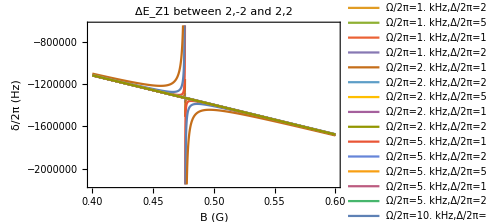

```mathematica
ΩdressTable = 2π{1,2,5,10,20}kHz;
ΔdressTable = 2π{1,2,5,10,20}MHz;
(*DressingTable = Transpose@{ΩdressTable,ΔdressTable};*)
DressingTable =Flatten[Table[{ΩdressTable[[i]],ΔdressTable[[j]]},{i,Range[Length[ΩdressTable]]},{j,Range[Length[ΔdressTable]]}],1];
Plot[Evaluate[Array[((ΔEqubit/.{Ωdress->DressingTable[[#,1]],Δdress->DressingTable[[#,2]]}))/( 2π)/.B->Bdc G&,Length[DressingTable]]],{Bdc,0.4,0.6},FrameLabel->{"B (G)","δ/2π (Hz)"},PlotLabel->"ΔE_Z1 between 2,-2 and 2,2",PlotLegends->Array[StringForm["Ω/2π=`` kHz,Δ/2π=`` MHz",Round[DressingTable[[#,1]]/(2π kHz),.01],Round[DressingTable[[#,2]]/(2π MHz),.01]]&,Length[DressingTable]]]
```

```mathematica
DressingTable =Flatten[Table[{ΩdressTable[[i]],ΔdressTable[[j]]},{i,Range[Length[ΩdressTable]]},{j,Range[Length[ΔdressTable]]}],1];
Plot[Evaluate[Array[((ΔEqubit/.{Ωdress->DressingTable[[#,1]],Δdress->DressingTable[[#,2]]}))/( 2π)/.B->Bdc G&,Length[DressingTable]]],{Bdc,0.4,0.6},FrameLabel->{"B (G)","δ/2π (Hz)"},PlotLabel->"ΔE_Z1 between 2,-2 and 2,2",PlotLegends->Array[StringForm["Ω/2π=`` kHz,Δ/2π=`` MHz",Round[DressingTable[[#,1]]/(2π kHz),.01],Round[DressingTable[[#,2]]/(2π MHz),.01]]&,Length[DressingTable]]]
```

-Graphics-

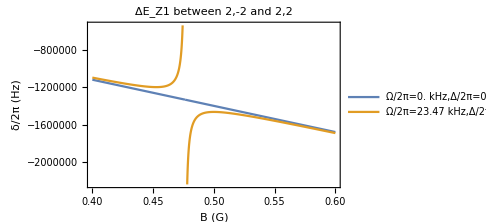

```mathematica
ΩdressTable = 2π{0,23.47}kHz;
ΔdressTable = 2π{0,1}MHz;
DressingTable = Transpose@{ΩdressTable,ΔdressTable};
(*DressingTable =Flatten[Table[{ΩdressTable[[i]],ΔdressTable[[j]]},{i,Range[Length[ΩdressTable]]},{j,Range[Length[ΔdressTable]]}],1];*)
Plot[Evaluate[Array[((ΔEqubit/.{Ωdress->DressingTable[[#,1]],Δdress->DressingTable[[#,2]]}))/( 2π)/.B->Bdc G&,Length[DressingTable]]],{Bdc,0.4,0.6},FrameLabel->{"B (G)","δ/2π (Hz)"},PlotLabel->"ΔE_Z1 between 2,-2 and 2,2",PlotLegends->Array[StringForm["Ω/2π=`` kHz,Δ/2π=`` MHz",Round[DressingTable[[#,1]]/(2π kHz),.01],Round[DressingTable[[#,2]]/(2π MHz),.01]]&,Length[DressingTable]]]
```

```mathematica
(*pick a dressing detuning and bias, solve for the correct Rabi frequency*)
Boffset=0.5G;
Ωsoln=Chop[Values[Assuming[Ωdress>0,NSolve[{(D[ΔEqubit,B]/.{B->Boffset,Δdress->2π 1 MHz})==0},{Ωdress},Reals]]]];
Ωsoln/(2π kHz)
(*{Δsoln,Ωsoln}=Transpose@Chop[Values[Assuming[Ωdress>0,NSolve[{(D[ΔEqubit,B]/.{B->Boffset,Δdress->2π 1 MHz})==0},{Ωdress},Reals]]]];*)
(*Print["Boffset=",Boffset/G];
Print[DressingTable=Transpose@{Ωsoln,Δsoln};
Join[{{"Ωdress/2π (kHz)","Δdress/2π (MHz)"}},Transpose@{Ωsoln/(2π kHz),Δsoln/(2π MHz)}]//TableForm];*)
```

{{-23.4711},{23.4711}}

### coherence for the magnetically sensitive states

Run one of the cells above to define ΔEqubit.

```mathematica
T2starTableNoDressing={};
σBTable={0.1,0.05,0.01,0.005,0.001}G;
For[i=1,i<Length[σBTable]+1,i++,
σB=σBTable[[i]];
Clear[ΔE];
Boffset=0.5G;
Ω0=Δ0=0;
ΔE[B_]=ΔEqubit/.{Ωdress->Ω0,Δdress->Δ0};(*units of angular frequency*)
"σΔE (Hz)";
σΔE=StandardDeviation[Map[ΔE,RandomVariate[NormalDistribution[Boffset,σB],100000]]/(2π)];
StringForm["T2^*=`` s, B_bias=`` G, Ω_dress/2π=`` kHz, Δ_dress/2π=`` MHz, σ_B=`` G", (√2)/σΔE,Boffset/G,Ω0/(2π kHz),Δ0/(2π MHz),σB/G];
AppendTo[T2starTableNoDressing,(√2)/σΔE];
];
```

```mathematica
T2starTableDressing={};
σBTable={0.1,0.05,0.01,0.005,0.001}G;
For[i=1,i<Length[σBTable]+1,i++,
σB=σBTable[[i]];
Clear[ΔE];
Boffset=0.5G;
Ω0=2π 23.471077974401425kHz;
Δ0=2π 1 MHz;
ΔE[B_]=ΔEqubit/.{Ωdress->Ω0,Δdress->Δ0};(*units of angular frequency*)
"σΔE (Hz)";
σΔE=StandardDeviation[Map[ΔE,RandomVariate[NormalDistribution[Boffset,σB],100000]]/(2π)];
StringForm["T2^*=`` s, B_bias=`` G, Ω_dress/2π=`` kHz, Δ_dress/2π=`` MHz, σ_B=`` G", (√2)/σΔE,Boffset/G,Ω0/(2π kHz),Δ0/(2π MHz),σB/G];
AppendTo[T2starTableDressing,(√2)/σΔE];
];
```

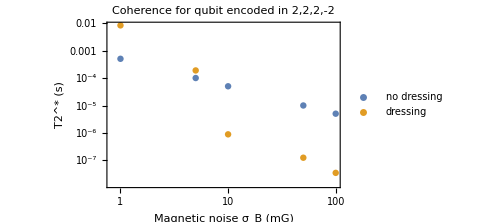

```mathematica
ListLogLogPlot[{Transpose@{10^3 σBTable/G,T2starTableNoDressing},Transpose@{10^3 σBTable/G,T2starTableDressing}},FrameLabel->{"Magnetic noise σ_B (mG)","T2^* (s)"},PlotLabel->"Coherence for qubit encoded in 2,2,2,-2",PlotLegends->{"no dressing","dressing"}]
```

```mathematica
"T2^* for 1 mG noise (s):"
"no dressing"
T2starTableNoDressing[[-1]]
"dressing"
T2starTableDressing[[-1]]
```

T2^* for 1 mG noise (s):

no dressing

0.000506601

dressing

0.00821798

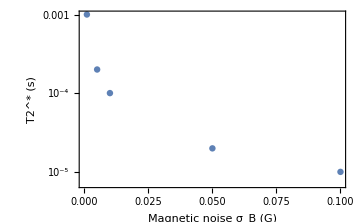

```mathematica
ListLogPlot[Transpose@{σBTable/G,T2starTable},FrameLabel->{"Magnetic noise σ_B (G)","T2^* (s)"}]
```

## Slowly rotating magnetic field

Suppose we prepare the atom in a particular magnetic hyperfine state mF then slowly rotate the bias field. How slowly do we need to rotate the field in order to ensure the state ends in mF in the final new basis? For the J=1/2 ground state of 87Rb, the energy of a spin flip is ~ ℏω_HF with ω_HF/2π = 6.834 GHz. The adiabatic theorem of quantum mechanics (see e.g. Griffiths QM Sec. 10.1) says that if the Hamiltonian evolves much slower than ω_HF then if the spin is initially aligned to the magnetic field, it will stay in that state wrt to the new basis (i.e. it will remain aligned to the field) as the field evolves. 

Below we can directly simulate the Schrodinger equation for this situation for a state of interest, such as the superposition states relevant to the Rb quantum network experiment.

```mathematica
BuildSchroedingerSystem[H_,psi0_]:=Module[
{hamiltonian=H,ψ0=psi0,ψ,statelength,eqs,ics,sys,P,i},
statelength = Length[ψ0];
ψ = Array[Subscript[P, #][t]&,statelength];
eqs = {};(*system to solve*)
ics = {};(*initial conditions*)
For[i=1,i<statelength+1,i++,
AppendTo[eqs,D[ψ[[i]],t]==-ⅈ (hamiltonian.ψ)[[i]]];
AppendTo[ics,(ψ[[i]]/.t->0)==ψ0[[i]]];
];
sys = Flatten@Join[eqs,ics];
{ψ,sys}
]
(*this expression is wrong for nonzero theta, so I likely messed up the sum over projections somehow. HFZ1MatElemRotated[I_,J_,gJ_,{F_,mF_},{FF_,mFF_},Bz_,θ_]:=μB Bz Quiet[ Sum[WignerD[{FF,mFF,nFF},θ]WignerD[{F,nF,mF},θ]ClebschGordan[{F,nF},{1,0},{FF,nFF}],{nF,-F,F},{nFF,-FF,FF}] √(2 F +1)(-1)^(1+J+I)(gJ (-1)^F √(J (J+1)(2 J+1))SixJSymbol[{J,I,F},{FF,1,J}]+
gI(-1)^FF √(I(I+1)(2I+1))SixJSymbol[{I,J,F},{FF,1,I}])];*)
(*--units--; for frequency units in GHz, our time unit is in ns*)
ms=10^6;
μs=10^3;
ns=1;
G=10^-4;(*T/G*)
(*--quantum numbers, Lande g factors, |F,mF> states--*)
S = 1/2; 
L = 0; 
J = 1/2;
gJ=gL(J(J+1)+L(L+1)-S(S+1)
+gS(J(J+1)-L(L+1)+S(S+1)))/(2J(J+1));
gF[F_]:= (gJ(F(F+1)+J(J+1)-INuc(INuc+1))
+gI(F(F+1)-J(J+1)+INuc(INuc+1)))/(2F(F+1));
states = Flatten[Table[Table[{F,mF},{mF,-F,F}],{F,{2,1}}],1];
dim = Length[states];
(*"states:"
Array[KetForm[states[[#]]]&,dim]*)
"states ordered by low-field energy"
states=Join[Reverse[Array[states[[#+5]]&,3]],Array[states[[#]]&,5]];
{F,mF}=Transpose@states;
stateLegend[i_:1,j_:-1]:=LineLegend[Array[KetForm[states[[#]]]&,dim][[i;;j]],LabelStyle->Directive[Black,FontSize->10]];
Array[KetForm[states[[#]]]&,dim]
```

states ordered by low-field energy

{1,1,1,0,1,-1,2,-2,2,-1,2,0,2,1,2,2}

Because of the finite bias field, the state we start in, |F’,m’>  , is really superposition of the states with zero field,|F',m'=m> = |F=F',m=m'>+∑_(F,m) α_(F,m)|F,m> where the unprimed states are the zero-field states. So to compare the state as it evolves with the initial state, we will first find the eigenvector expansion of |F’,m’> in terms of the undressed states.

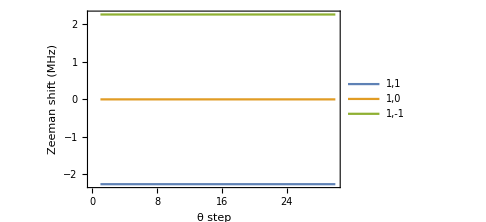

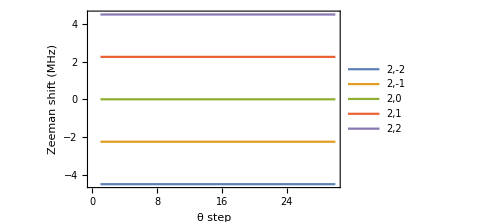

```mathematica
Clear[θ,θf,tmax,Bz,θ];
Bz=3.23G;
θf=34.95*π/180;(*final angle of the field after a rotation about y*)
tmax=1μs;
θ=θf (1-Cos[π/2 t/tmax]^2);
(*θ=t(*θf t/tmax*);*)

Table[Subscript[HZ, i,j]=Subscript[HZ, j,i]=JToGHz[HFZ1MatElem[INuc,J,gJ,states[[i]],states[[j]],Bz]],{i,1,dim},{j,i,dim}];
HZ1=Table[Subscript[HZ, i,j],{i,1,dim},{j,1,dim}];
Dmatrix=Table[KroneckerDelta[F[[i]],F[[j]]]WignerD[{F[[i]],mF[[i]],mF[[j]]},θ],{i,1,dim},{j,1,dim}];
HAtom = Array[0&,{dim,dim}];
Array[(HAtom[[#,#]]=Rb87fGHz[{5,0,1/2,F[[#]]}])&,dim];
steps=30;
(*tTable=Range[0,tmax,tmax/steps];*)
tTable=Range[0,tmax,tmax/steps];
energySoln={};
For[i=1,i<steps+1,i++,
WD=Dmatrix/.t->tTable[[i]];
HTotal=HAtom + WD†.HZ1.WD;
{evals,evecs}=Eigensystem[HTotal(*/.t->tTable[[i]]*)];
epairs=SortBy[Transpose@{evals,evecs},#[[1]]&];
If[i==1,evecs0=(Transpose@epairs)[[2]]];(*Zeeman shifted eigenvectors at t=0*)
AppendTo[energySoln,(Transpose@epairs)[[1]]];
(*AppendTo[evecsSorted,evecs]*)
]
energies=Transpose@energySoln;
(*Verify that the instantaneous eigen-energies do not depend on the B field angle*)
ListPlot[(energies[[;;3]]-Rb87fGHz[{5,0,1/2,1}])10^3,Joined->True,FrameLabel->{"θ step","Zeeman shift (MHz)"},PlotLegends->stateLegend[1,3]]
ListPlot[(energies[[4;;]]-Rb87fGHz[{5,0,1/2,2}])10^3,Joined->True,FrameLabel->{"θ step","Zeeman shift (MHz)"},PlotLegends->stateLegend[4]]
```

```mathematica
Dmatrix/.t->tmax//N//MatrixForm
```

(0.909826 | 0.405074 | 0.0901739 | 0. | 0. | 0. | 0. | 0.
-0.405074 | 0.819652 | 0.405074 | 0. | 0. | 0. | 0. | 0.
0.0901739 | -0.405074 | 0.909826 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0.827784 | -0.521204 | 0.200962 | -0.0516571 | 0.00813133
0. | 0. | 0. | 0.521204 | 0.581656 | -0.575075 | 0.237996 | -0.0516571
0. | 0. | 0. | 0.200962 | 0.575075 | 0.507745 | -0.575075 | 0.200962
0. | 0. | 0. | 0.0516571 | 0.237996 | 0.575075 | 0.581656 | -0.521204
0. | 0. | 0. | 0.00813133 | 0.0516571 | 0.200962 | 0.521204 | 0.827784)

```mathematica
(*--setup and solve the Schrodinger equation*)


ψ0 = evecs0[[1]];(*start in |F=1,m=1> of the dressed atom, expressed in the zero-field basis*)
HTotal=HAtom+Dmatrix†.HZ1.Dmatrix;
{ψ,eqs}=BuildSchroedingerSystem[HTotal,ψ0];
{time,soln}= Timing[First@NDSolve[eqs, ψ, {t,0,tmax}]];
ψsoln=Transpose[soln[[;;,2]]];
Print[StringForm["Time to run sim: `` s",time]];
```

Time to run sim: 0.421875 s

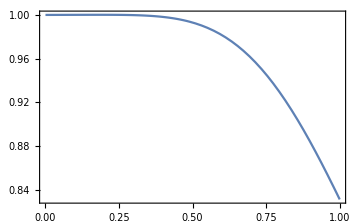

```mathematica
scale=tmax;
Plot[Abs[Dot[ψsoln,ψ0]]^2/.t->τ scale,{τ,0,tmax/scale}]
```

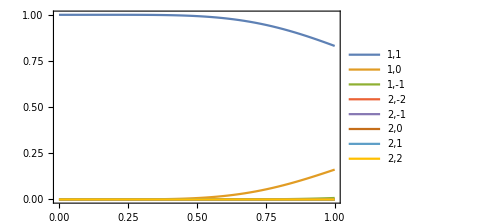

```mathematica
Plot[Evaluate[Array[Abs[soln[[#,2]]]^2/.t->τ scale&,dim]],{τ,0,tmax/scale},PlotLegends->stateLegend[],PlotRange->All]
```

```mathematica
evecs0[[1]]
```

{-1.,0.,0.,0.,0.,0.,0.000571986,0.}

Start in an equal superposition of the F=1; -1,+1 states, then do the evolution over varying amounts of time and plot the fidelity to the target to the state in the final basis. Adiabatic theorem: ramp much slower than the energy difference between the states:

```mathematica
"make ramp time >> 2π/ωQubit (ns) ="
τQ=2π/(evals[[3]]-evals[[1]])
```

make ramp time >> 2π/ωQubit (ns) =

1388.22

Time to run step 1: 0.328125 s

Time to run step 2: 1.76563 s

Time to run step 3: 3.59375 s

Time to run step 4: 17.9375 s

Time to run step 5: 34.5469 s

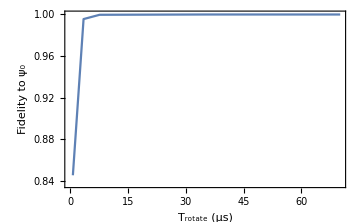

```mathematica
ψ0=1/(√2)(evecs0[[1]]+evecs0[[3]]);
τQ=2π/(evals[[3]]-evals[[1]]); (*qubit oscillation period in ns*)
tsteps=τQ/2*{1,5,11,51,101}(*{μs,5μs,10μs,50μs,100μs}*);(*should go an odd number of half periods*)
Clear[θ]
fidelity={};
solnList={};
Bz=3.23G;
θf=34.95*π/180;(*final angle of the field after a rotation about y*)
Table[Subscript[HZ, i,j]=Subscript[HZ, j,i]=JToGHz[HFZ1MatElem[INuc,J,gJ,states[[i]],states[[j]],Bz]],{i,1,dim},{j,i,dim}];
HZ1=Table[Subscript[HZ, i,j],{i,1,dim},{j,1,dim}];
(*get the target state at the end of the rotation*)
Dmatrix=Table[KroneckerDelta[F[[i]],F[[j]]]WignerD[{F[[i]],mF[[i]],mF[[j]]},θ],{i,1,dim},{j,1,dim}];
HTotal=HAtom+(Dmatrix†.HZ1.Dmatrix)/.θ->θf;
{evals,evecs}=Eigensystem[HTotal];
epairs=SortBy[Transpose@{evals,evecs},#[[1]]&];
evecs=(Transpose@epairs)[[2]];
ψtarget=1/(√2)(evecs[[1]]+evecs[[3]]);
For[i=1,i<Length[tsteps]+1,i++,
Clear[θ,tmax,θ];
tmax=tsteps[[i]];
θ=θf (1-Cos[π/2 t/tmax]^2);
Dmatrix=Table[KroneckerDelta[F[[i]],F[[j]]]WignerD[{F[[i]],mF[[i]],mF[[j]]},θ],{i,1,dim},{j,1,dim}];
HTotal=HAtom+Dmatrix†.HZ1.Dmatrix;
{ψ,eqs}=BuildSchroedingerSystem[HTotal,ψ0];
{time,soln}= Timing[First@NDSolve[eqs, ψ, {t,0,tmax},Method->"ExplicitRungeKutta"]];
ψsoln=Transpose[soln[[;;,2]]];(*solution is now a state vector*)
AppendTo[solnList,ψsoln];
Print[StringForm["Time to run step ``: `` s",i,time]];
AppendTo[fidelity,Abs[Dot[ψsoln*,ψtarget]]^2/.t->tmax];
]
ListPlot[Transpose@{tsteps/μs,fidelity},FrameLabel->{"T_rotate (μs)","Fidelity to ψ_0"},Joined->True]
```

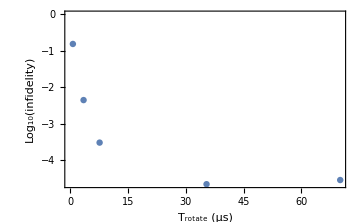

```mathematica
ListPlot[Transpose@{tsteps/μs,Log10[1-fidelity]},FrameLabel->{"T_rotate (μs)","Log_10(infidelity)"},PlotRange->Automatic(*{0,.005}*)]
```

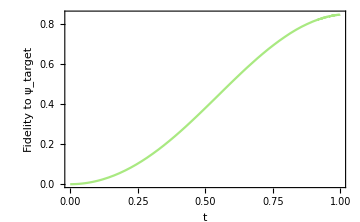

1

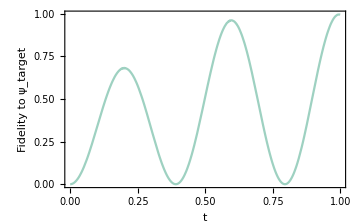

2

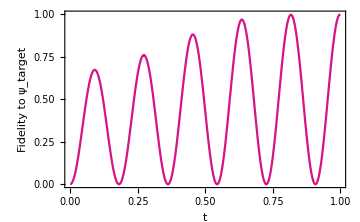

3

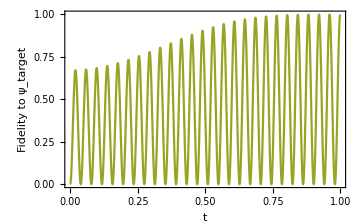

4

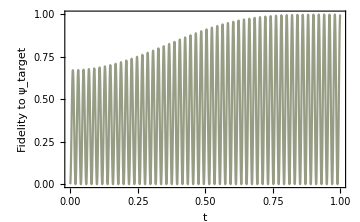

```mathematica
colors=Array[RGBColor[RandomReal[],RandomReal[],RandomReal[]]&,tsteps//Length];
(*Print the fidelity to the target state vs time in real units, one at a time*)
plts={};
For[i=1,i<(tsteps//Length)+1,i++,
Print[Plot[Abs[Dot[solnList[[i]]*,ψtarget]]^2/.t->τ tsteps[[i]],{τ,0,1},PlotStyle->colors[[i]],FrameLabel->{"t","Fidelity to ψ_target"},PlotRange->All(*{{0,tsteps[[-1]]},{0,1.05}}*),PlotLegends->StringForm["`` μs, F=``",tsteps[[i]]/μs,fidelity[[i]]]]];
Print[i]
]
```

1

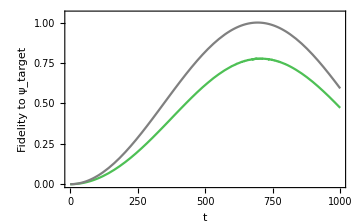

```mathematica
i=1
Plot[{Abs[Dot[solnList[[i]]*,ψtarget]]^2,Sin[(evals[[3]]-evals[[1]])/2 t]^2},{t,0,tsteps[[i]]},PlotStyle->{colors[[i]],Gray},FrameLabel->{"t","Fidelity to ψ_target"},PlotRange->{{0,tsteps[[i]]},{0,1.05}},PlotLegends->StringForm["`` μs",tsteps[[i]]/μs]]
```

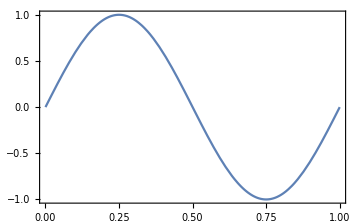

```mathematica
ω=2π;
Plot[Sin[ω t],{t,0,1}]
```

```mathematica
2π/ω
```

1

1388.22

```mathematica
evals
```

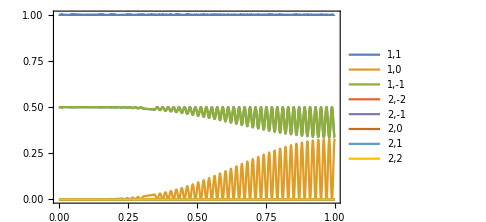

```mathematica
scale=tmax;
population=Array[Abs[soln[[#,2]]]^2/.t->τ scale&,dim];
Show[Plot[Evaluate[population],{τ,0,tmax/scale},PlotLegends->stateLegend[],PlotRange->All],Plot[Total[population],{τ,0,tmax/scale},PlotLegends->"Total"]]
```

## testing

```mathematica
{evals,evecs}=Eigensystem[HTotal/.t->tmax];
epairs=Transpose@{evals,evecs};
evalsSorted={};
evecsSorted={};
For[i=1,i<dim+1,i++,
{eval,evec}=SortBy[epairs,Abs[Dot[#[[2]],Array[Boole[#==i]&,dim]]]&][[-1]];
AppendTo[evalsSorted,eval];
AppendTo[evecsSorted,evec];
]
evals=evalsSorted;
evecs=evecsSorted;
```

```mathematica
Abs[evecs[[-1]].ψ0]^2
```

0.735487

```mathematica
1/(6.834*10^9)
```

1.46327×10^-10

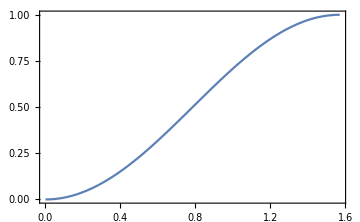

```mathematica
Plot[ 1-Cos[θ]^2,{θ,0,π/2}]
```

```mathematica
states
```

{{2,-2},{2,-1},{2,0},{2,1},{2,2},{1,-1},{1,0},{1,1}}

```mathematica
Bz
```

0.000362

```mathematica
data=Table[JToGHz[HFZ1MatElemRotated[INuc,J,gJ,states[[i]],states[[j]],10Bz,0]],{i,1,dim},{j,1,dim}]
```

{{-0.0505245,0.,0.,0.,0.,0.,0.,0.},{0.,-0.0252622,0.,0.,0.,0.0438427,0.,0.},{0.,0.,0.,0.,0.,0.,0.0506251,0.},{0.,0.,0.,0.0252622,0.,0.,0.,0.0438427},{0.,0.,0.,0.,0.0505245,0.,0.,0.},{0.,0.0438427,0.,0.,0.,0.0253629,0.,0.},{0.,0.,0.0506251,0.,0.,0.,0.,0.},{0.,0.,0.,0.0438427,0.,0.,0.,-0.0253629}}

```mathematica
JToGHz[μB Bz]
```

0.00505942

```mathematica
data//MatrixForm
```

(-0.0505245 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -0.0252622 | 0. | 0. | 0. | 0.0438427 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.0506251 | 0.
0. | 0. | 0. | 0.0252622 | 0. | 0. | 0. | 0.0438427
0. | 0. | 0. | 0. | 0.0505245 | 0. | 0. | 0.
0. | 0.0438427 | 0. | 0. | 0. | 0.0253629 | 0. | 0.
0. | 0. | 0.0506251 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0.0438427 | 0. | 0. | 0. | -0.0253629)

```mathematica
Table[KetForm[states[[i]]]->KetForm[states[[j]]],{i,1,dim},{j,1,dim}]//MatrixForm
```

(2,-2→2,-2 | 2,-2→2,-1 | 2,-2→2,0 | 2,-2→2,1 | 2,-2→2,2 | 2,-2→1,-1 | 2,-2→1,0 | 2,-2→1,1
2,-1→2,-2 | 2,-1→2,-1 | 2,-1→2,0 | 2,-1→2,1 | 2,-1→2,2 | 2,-1→1,-1 | 2,-1→1,0 | 2,-1→1,1
2,0→2,-2 | 2,0→2,-1 | 2,0→2,0 | 2,0→2,1 | 2,0→2,2 | 2,0→1,-1 | 2,0→1,0 | 2,0→1,1
2,1→2,-2 | 2,1→2,-1 | 2,1→2,0 | 2,1→2,1 | 2,1→2,2 | 2,1→1,-1 | 2,1→1,0 | 2,1→1,1
2,2→2,-2 | 2,2→2,-1 | 2,2→2,0 | 2,2→2,1 | 2,2→2,2 | 2,2→1,-1 | 2,2→1,0 | 2,2→1,1
1,-1→2,-2 | 1,-1→2,-1 | 1,-1→2,0 | 1,-1→2,1 | 1,-1→2,2 | 1,-1→1,-1 | 1,-1→1,0 | 1,-1→1,1
1,0→2,-2 | 1,0→2,-1 | 1,0→2,0 | 1,0→2,1 | 1,0→2,2 | 1,0→1,-1 | 1,0→1,0 | 1,0→1,1
1,1→2,-2 | 1,1→2,-1 | 1,1→2,0 | 1,1→2,1 | 1,1→2,2 | 1,1→1,-1 | 1,1→1,0 | 1,1→1,1)

```mathematica
Image[data,ImageSize->Medium]
```

-Graphics-

```mathematica
Table[{i,j},{i,1,dim},{j,i,dim}]
```

{{{1,1},{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8}},{{2,2},{2,3},{2,4},{2,5},{2,6},{2,7},{2,8}},{{3,3},{3,4},{3,5},{3,6},{3,7},{3,8}},{{4,4},{4,5},{4,6},{4,7},{4,8}},{{5,5},{5,6},{5,7},{5,8}},{{6,6},{6,7},{6,8}},{{7,7},{7,8}},{{8,8}}}

```mathematica
Rb87fGHz[{5,1,3/2,3}]-Rb87fGHz[{5,0,1/2,2}]
```

384228.

$Aborted

```mathematica
Assuming[ω∈Reals&&ωE∈Reals&&Ω∈Reals,Eigenvalues[({{ω, Ω ⅇ^(-ⅈ (ω-ωE)t)}, {Ω ⅇ^(ⅈ (ω-ωE)t), 0}})]]//FullSimplify
```

{1/2 (ω-√(ω^2+4 Ω^2)),1/2 (ω+√(ω^2+4 Ω^2))}

```mathematica
Assuming[Δ∈Reals&&Ω∈Reals,Eigenvalues[({{Δ, Ω ⅇ^(-ⅈ Δ t)}, {Ω ⅇ^(ⅈ Δ t), 0}})]]//FullSimplify
```

{1/2 (Δ-√(Δ^2+4 Ω^2)),1/2 (Δ+√(Δ^2+4 Ω^2))}